# Surface CRNs for k-coloring of graphs

Executive summary:

We are interested in how computational chemical reaction networks can (or cannot) effectively exploit parallelism to find solutions faster.  This includes questions of algorithm design (how do we effectively explore the search space in the first place?), volume-dependence (does just having more of the same stuff get you faster computation, or slower computation, or it depends?), and spatial geometry (do we just pour stuff into a region, or can we design the initial spatial layout?).

Investigating these and related issues requires some foundations and some test problems.  For test problems, we have considered 3-SAT, K-coloring, and Circuit-SAT.  Foundational issues include how to test and quantify CRN algorithms.   You’ll find a few steps in that direction here, perhaps most importantly including methods to generate hard K-coloring examples and obtain comparison timings for conventional algorithms that solve them.  (My 2019 paper did this for 3-SAT, as can be found in the paper’s accompanying code.)

## Simulator code: execute all initialization cells in “FastSurfaceCRNs.nb”

Just do it.  Then you can execute initially cells in this notebook.

## Surface diffusion version of well-mixed CRN for graph coloring from “SolutionAssignment6.nb”

Let’s briefly return to the question of volume scaling -- how to exploit more molecules to do more computation.  We saw at the start of this notebook that the naive ColoringCRN from the class homework did not scale well when more molecules are involved.   I similarly tested the WalkSATCRN in the past, and while it seemed to tolerate slightly higher copy numbers, it also ultimately bogged down.   I have therefore been curious whether spatial inhomogeneity -- as in a surface CRN -- might allow the chemical system to take advantage of the extra molecules. If 1 copy of each relevant molecule occupies area V at an appropriate concentration and with all species diffusing just barely fast enough for that region to remain well-mixed, then area V in the surface CRN should replicate the behavior (i.e. also solve the 3-SAT problem) of the formally well-mixed stochastic CRN.  That is, although the surface CRN will be much slower to simulate because now each diffusion step is explicitly modelled, the “time stamp” of the surface CRN and of the well-mixed stochastic CRN should be the same (on average) in both models when the problem is solved.  (The surface CRN won’t “halt” because the diffusion reactions will always be active, but the identity of the species will stop changing.)  Then, the question is that if we now use more molecules without otherwise changing the CRN, will the spatial inhomogeneity automatically allow us to effectively exploit the chemical parallelism? 

There are two effects we might hope for. The first effect: If we scale up the number of molecules by m, so the new volume V' = m V, then because diffusion rates were set such that they only just barely mix area V, we can consider the surface to have roughly m different regions that may have different species present and thus may represent different candidate solutions to the SAT problem. Suppose, after a certain amount of time, one of these regions finds the solution.   But it’s surrounded by regions that have incorrect or partial solutions.  Either (a) the region with a correct solution influences its neighbors (by diffusion) to also get nudged into finding the correct solution, and thus the correct region expands eventually to fill the whole space, or (b) the CRN dynamics are that the neighboring regions with incorrect or partial solutions influence the region with a correct solution, messing up its solution so that it gets worse and worse, eventually completely loosing track of all correct bits.   My intuition is that some CRNs (those that are doing a not-effectively-biased random walk, such as the CircuitSATCRN and FormulaSATCRN from my 2019 paper, and the ColoringCRN from BE/CS 191a homework 6) will be of type (b), whereas other CRNs (those that effectively bias themselves toward better solutions, such as WalkSATCRN) will by of type (a).  If so, then the type (a) CRNs will presumably have some velocity for the “correct solution” wavefront propagation, so once it’s found, the solution wave will propagate across the entire surface in time proportional to the width of the surface, which is O(√m).   In 3D, it would be O(m^(1/3)).   Supposing that the original well-mixed CRN would find a solution in average time-stamp T, then we might expect that some region of the surface will find a solution in perhaps expected time T/m, and thus the entire surface has the correct answer by time T/m+O(√m).   This would be making good, full use of the parallelism, as the first part of the term would dominate.  (Obviously, the surface CRN simulations on an electronic computer would be much slower than simulating the well-mixed stochastic CRN, but that’s not the point: the question is asking how real chemical systems can best exploit the resources at their disposal.)

The second effect we might hope for is the one that Cheeseman mentioned, which is that perhaps if 90% of initial states will get trapped in some super-long exploration of bad configurations, while 10% of initial states will find a solution in reasonable time, then parallel exploration on the surface (if the type-(a) behavior holds) would be likely to have at least one region find a correct solution in reasonable time so long as m>>10.   This would be a different way in which the surface parallelism speeds up searches -- primarily by avoiding the unfortunate long-tailed exploration.

The problem with exploring the above ideas about chemical parallelism with the WalkSATCRN is that it used trimolecular reactions, which are not natural for the surface CRN model.   One could implement them using multiple bimolecular reactions, but it would be a bit awkward and introduce even more simulation slow-down on top of the cost of explicit simulation of diffusion.  In contrast, the BE/CS 191a homework 6 ColoringCRN uses only unimolecular and bimolecular reactions, so we really can “just try it”.   To wit:

We’ll use the same CRN as above, augmented with a “solution” species S and diffusion reactions for each species to diffuse through S.  With an initial state consisting of about 50% diffusion, and diffusion rates comparable with reaction rates (maybe a bit less) we can ensure that eventually every vertex will talk to every other vertex.  However, this CRN will not halt -- it will just get to a state from whence all further reactions are exclusively diffusion, and no colorings change.   Given a graph with N vertices and a target multiplicity m, which entails N m molecules, we could put them in a 1D, 2D, or 3D space with, say, approximately 2 N m sites.

```mathematica
(* same as in class *)
G1 = Graph[{"a","b","c","d","e"},{"a"<->"b","a"<->"c","a"<->"d","a"<->"e","b"<->"c","b"<->"d","b"<->"e","c"<->"d","c"<->"e"}];
G2=Graph[{1,2,3,4,5,6},{1<->2,1<->3,1<->4,2<->3,2<->4,2<->5,3<->6,4<->5,5<->6}];
G3=PetersenGraph[7,6];
G4 = Graph[{1,2,3,4,5,6},{1<->4,1<->3,4<->3,5<->3,6<->3,4<->5,5<->6,2<->6,3<->2,4<->6,1<->5,2<->5}];
ColoringCRN[G_,k_]:=Flatten[Join[
Table[rxn[V[v],V[v,c],1],{v,VertexList[G]},{c,Range[k]}],  (* a vertex without a color will randomly choose a color *)Table[rxn[V[First[e],c]+V[Last[e],c],V[First[e]]+V[Last[e]],1],{e,EdgeList[G]},{c,Range[k]}], (* conflicting edges recolor *)
Table[conc[V[v],1],{v,VertexList[G]}] (* each vertex starts uncolored *)
]]
```

```mathematica
SurfaceColoringCRN[G_,k_,diff_]:=With[{crn=Cases[ColoringCRN[G,k],Except[_conc]]},
Flatten[Join[
crn,
Table[rxn[V[v]+S,S+V[v],diff],{v,VertexList[G]}],
Table[rxn[V[v,c]+S,S+V[v,c],diff],{v,VertexList[G]},{c,Range[k]}]
]]]
SurfaceColoringSpace[G_,k_,m_,dim_]:=Module[{n=Ceiling[(2 Length[VertexList[G]] m)^(1/dim)],N=Length[VertexList[G]],space},
space=ArrayReshape[
Flatten[Table[Table[V[v],{v,VertexList[G]}],m]~Join~Table[S,n^dim-m N ]],
Table[n,dim]]
]
SurfaceColoringRules[G_,k_]:={S->White,V[v_]:>Gray,V[v_,c_]:>{Red,Green,Blue,Yellow}[[c]]}
SurfaceColoringAnalysis[space_,vertices_]:=With[{mols=Sort[Flatten[space]]},Table[Cases[mols,V[v,c_]:>c],{v,vertices}]]
```

```mathematica
Dynamic[{ArrayPlot[surface,ColorRules->surfacecoloring,PlotLabel->surfacetime],SurfaceColoringAnalysis[surface,surfaceV]}]
```

```mathematica
surface//MatrixForm
```

```mathematica
With[{G=G2,k=4,m=4,diff=0.1,dim=2,dt=1},
surfaceV=VertexList[G];
surfaceCRN=SurfaceColoringCRN[G,k,diff];
surface=SurfaceColoringSpace[G,k,m,dim];
surfacecoloring=SurfaceColoringRules[G,k];
surfacetime=0;
While[True,surface=RunSurfaceCRN[surfaceCRN,surface,dt];surfacetime+=dt]
]
```

This is not fast!  Sure, using RunFasterSurfaceCRN would make it faster, but the more telling issue is that the multiple copies of each vertex species have trouble agreeing with each other.  Since there will always be at least k! distinct (but isomorphic) colorings, if any exist, one can see how it might be hard for one to dominate.  In fact, we sometimes see that (maybe by time stamp 20,000 or more) the system here converges to a “combination” coloring where multiple colors are assigned to some of the vertices, yet nonetheless no conflicts arise.  In principle, that also solves the problem -- but it also illustrates just how hard it is to converge.  

In the context of the arguments above, what this brings up is that we don’t just have to worry about regions of “correct solution” vs regions of “incorrect or partial solutions” and which way the boundary moves, but we also have to worry about the interface between two regions, both of which are correct but with different solutions.   It’s hard to argue that we should expect a systematic bias in that case. 

As mentioned above, I have been imagining that the WalkSATCRN, in contrast to the simpler FormulaSATCRN that doesn’t invoke a bias toward good solutions, would have the property in spatial systems that conflicts between areas with a good solution would preferentially expand into poor solutions, sort of like Toom’s rule, or sea anemone colonies.   It seems reasonable to tentatively conclude here that the naive ColoringCRN doesn’t have this property... or maybe it does, with large enough m, or slow enough diffusion, but we can’t see it with the current parameters, even with the faster simulations below.  

(Also to think about: How can I change the coloring so that regions encoding different colorings can be clearly distinguished, so we can see the interface between regions representing different solutions?)

```mathematica
Dynamic[{
ArrayPlot[First[fsurface],ColorRules->fsurfacecoloring,PlotLabel->fsurfacetime],
Mean[1.0 #]&/@SurfaceColoringAnalysis[RevertFaster2Space[fsurface,fsurfaceCRN],fsurfaceV]
}]
```

```mathematica
With[{G=G2,k=4,m=1000,diff=0.1,dim=2},
fsurfaceV=VertexList[G];
fsurfaceCRNorig=SurfaceColoringCRN[G,k,diff];
fsurfaceorig=SurfaceColoringSpace[G,k,m,dim];
fsurfacecoloringorig=SurfaceColoringRules[G,k];

fsurfaceCRN=PreprocessFasterSurfaceCRN[fsurfaceCRNorig,{fsurfaceorig}];
fsurface=Convert2FasterSpace[{fsurfaceorig},fsurfaceCRN];
fsurfacecoloring=Convert2FasterColoring[ fsurfacecoloringorig,fsurfaceCRN]; (* this doesn't work for DelayedRules, alas *)
fsurfacetime=0;
]
```

```mathematica
With[{dt=100},While[True,fsurface=RunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];fsurfacetime+=dt]]
```

Concluding thoughts about surface CRNs:

It will be interesting to see if a TabuCol-inspired CRN uses  only unimolecular and bimolecular reactions, will it have a suitably stabilizing property to make the surface reaction-diffusion parallelism effective?

Or is there a natural way to modify the WalkSATCRN so as to just use unimolecular and biomolecular reactions, to demonstrate the effect (if it exists)?

We should take a moment to contrast the reaction-diffusion stochastic local search CRN behavior with other ways to use surface CRNs for stochastic local search, such as the surface CRN 3-coloring and 4-coloring CRNs.  The first point is that the reaction-diffusion approach uses (roughly) the same number of species and reactions as the well-mixed CRN for the same problem -- that is, a lot of species! -- but (we hope) has the potential to naturally exploit spatial parallelism.  This is valuable to know if (a) we want to understand the computational power of reaction-diffusion species, and/or (b) we think designing molecules that diffuse in solution is markedly easier than designing molecules that are affixed to a surface and move only “on command”.   The second point is that if we we are ready to exploit all the capabilities of surface CRNs, including non-diffusive species, then a single, fixed, relatively small set of reactions can solve all problems (for a given fixed K) by specifying the problem in the initial surface layout, and further, it can (we hope) make good use of parallelism by making multiple copies of the layout and integrating their answers.  The BE/CS 191a homework established the first point, while the second point remains to be worked out in detail.  Further, we have not yet established whether and how this layout-based approach can be computationally efficient, like the well-mixed WalkSATCRN is.  Matt’s Surface-Circuit-SAT construction may address this point.

The above was done prior to testing any of the more advanced well-mixed coloring CRNs, such as WalkColoringCRN.  We’re in a position now where we could explore whether those CRNs are diffusionally stable.  One way to test would be to start with a surface covered in M copies of each each species from a successful coloring solution, then flip just 1 molecules (or D molecules) to create coloring conflicts.  How long does it take for those conflicts to go away?   This is worth investigating.

## Surface layout graph coloring CRN from “SolutionAssignment6.nb”

The halting property is very nice, so of the two CRNs in the solution set, we’ll start with that one.  But it was unnecessary there to distinguish between the single-site vertex V and the surrounding vertex area v, so here we’ll simplify the CRN to just use the vertex region species v[c] and the edge species e[c].   We’ll also simplify it by always starting every vertex and edge in color 1.

```mathematica
SurfaceMapColoringCRN[k_]:=Union[Flatten[{
Table[If[c1=!=c2,
{ 
rxn[v[c1]+v[c2],v[c2]+v[c2],1],(* neighboring v must agree; if not, one randomly follows the other *)
rxn[v[c1]+e[c2],v[c1]+e[c1],1],(* v and neighboring e must agree; if not, one randomly follows the other *)
rxn[v[c1]+e[c2],v[c2]+e[c2],1],
rxn[e[c1]+e[c1],e[c1]+e[c2],0.01]    (* adjacent edge sites must be different; if not, one randomly changes *)
},{}],
{c1,1,k},{c2,1,k}]
}]]
MapColoringRules[k_]:=With[{colors={Red,Green,Lighter[Blue],Black}},
Flatten[Join[
{w->White},
Table[{v[i]->Darker[colors[[i]]],e[i]->Lighter[colors[[i]]]},{i,1,k}]
]]]
```

```mathematica
SurfaceMapColoringCRN[4]//MatrixForm
```

```mathematica
Length[SurfaceMapColoringCRN[4]]
```

48

```mathematica
mapG1={
{v,v,v,v,v,v,v,v,V,v,v,v,v,v,w},
{v,w,w,v,w,w,w,v,v,v,w,w,w,v,w},
{v,w,w,e,w,w,w,w,e,w,w,w,w,e,w},
{v,w,w,e,w,w,w,w,e,w,w,w,w,e,w},
{v,w,v,v,v,w,w,v,v,v,w,w,v,v,v},
{e,w,v,V,v,e,e,v,V,v,e,e,v,V,v},
{e,w,v,v,v,w,w,v,v,v,w,w,v,v,v},
{v,w,w,e,w,w,w,w,e,w,w,w,w,e,w},
{v,w,w,e,w,w,w,w,e,w,w,w,w,e,w},
{v,w,w,v,w,w,w,v,v,v,w,w,w,v,w},
{v,v,v,v,v,v,v,v,V,v,v,v,v,v,w}
}/. {V->v[1],v->v[1],e->e[1]};
mapG2={
{w,w,w,w,w,w,w,w,w,w,w,w,w,w},
{w,V,v,v,v,v,e,e,v,V,v,v,v,w},
{w,v,v,v,v,w,w,w,v,v,v,w,e,w},
{w,v,v,v,e,w,V,w,e,v,w,w,e,w},
{w,e,w,w,e,v,v,v,e,w,w,v,v,w},
{w,e,w,e,v,v,v,w,w,w,v,v,v,w},
{w,v,v,e,w,w,e,e,w,w,v,v,v,w},
{w,v,v,v,e,w,w,v,V,w,e,w,V,w},
{w,V,w,w,e,v,v,v,v,v,e,w,w,w},
{w,w,w,w,w,w,w,w,w,w,w,w,w,w}
}/. {V->v[1],v->v[1],e->e[1]};;
mapG3={
{w,w,w,e,e,v,v,v,v,v,V,v,v,v,v,v,e,e,w,w,w},
{w,v,v,v,w,w,w,w,w,v,v,v,w,w,w,w,w,v,v,v,w},
{w,v,V,v,e,e,w,w,w,w,e,w,w,w,w,e,e,v,V,v,w},
{v,v,v,v,w,v,v,v,w,w,e,w,w,v,v,v,w,v,v,v,v},
{v,w,w,w,w,v,V,v,w,v,v,v,w,v,V,v,w,w,w,w,v},
{v,w,w,w,e,v,v,v,w,v,V,v,w,v,v,v,e,w,w,w,v},
{e,w,w,w,e,w,w,e,e,v,v,v,e,e,w,w,e,w,w,w,e},
{e,w,w,v,v,v,w,w,w,w,w,w,w,w,w,v,v,v,w,w,e},
{v,w,w,v,V,v,v,e,w,w,w,w,w,e,v,v,V,v,w,w,v},
{v,w,e,v,v,v,w,e,w,w,w,w,w,e,w,v,v,v,e,w,v},
{v,v,e,w,w,w,v,v,v,w,w,w,v,v,v,w,w,w,e,v,v},
{V,v,w,w,w,e,v,V,v,v,e,w,v,V,v,e,w,w,w,v,V},
{v,v,e,w,w,e,w,v,v,w,e,v,v,v,w,e,w,w,e,v,v},
{w,w,e,v,v,v,w,w,w,w,w,w,w,w,w,v,v,v,e,w,w},
{w,w,w,v,V,v,v,v,v,e,e,v,v,v,v,v,V,v,w,w,w}
}/. {V->v[1],v->v[1],e->e[1]};;
```

```mathematica
With[{map=mapG3,k=4},
fsurfaceCRNorig=SurfaceMapColoringCRN[k];
fsurfaceorig=map;
fsurfacecoloringorig=MapColoringRules[k];
fsurfaceCRN=PreprocessFasterSurfaceCRN[fsurfaceCRNorig,{fsurfaceorig}];
fsurface=Convert2FasterSpace[{fsurfaceorig},fsurfaceCRN];
fsurfacecoloring=Convert2FasterColoring[ fsurfacecoloringorig,fsurfaceCRN]; (* this doesn't work for DelayedRules, alas *)
fsurfacetime=0;
]
```

```mathematica
Dynamic[ArrayPlot[First[fsurface],ColorRules->fsurfacecoloring,PlotLabel->fsurfacetime]]
```

```mathematica
haltedq=0;
With[{dt=0.1},While[haltedq==0,{{ddt,eventcount,haltedq},fsurface}=InfoRunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];fsurfacetime+=ddt]]
```

So it works and it’s reasonably fast.  Let’s generate random planar maps using a percolation approach: N x M vertices, with probability p for connecting a region to a von Neumann  neighbor via a “land bridge” to make them the same map region, and otherwise a probability q for creating an “edge” to the neighbor (unless it ends up being the same region as connected by land bridges) .  So between two lattice sites, probability p is a land bridge, probability (1-p)q is an edge, and probability (1-p)(1-q) is empty. The size of single-color regions now depends on the percolation parameter p.   For large enough p, these regions may bend around on themselves, and allowing a formal edge to be made between a region and another part of itself -- thus making the entire graph not colorable.   This being far too common, our code below goes to some lengths to identify and remove such edges.   While we’re at it, we construct a formal graph corresponding to the layout, so that we can use SatisfiableQ / MiniSAT to test colorability before asking our surface CRN to try it.

It would be a lot easier to just use a regular square grid or regular hexagonal grid, with a random subset of edges -- but any subset of a square grid is 2-colorable, and any subset of a hex grid is 3-colorable.  Granted, any subset of a planar graph is 4-colorable, yet it’s still interesting (and hard) to actually find a coloring.   Still, the land bridges in the random maps result in regions that permit arbitrary graphs, hence the NP-completeness of planar 3-colorability (cf Garey & Johnson, 1979) means we’re in the zone for genuinely hard decisions problems.

```mathematica
ColoringSAT[G_,k_]:=With[{v=VertexList[G],e=EdgeList[G]},
And@@Flatten[Join[
Table[!V[edge[[1]],c]||!V[edge[[2]],c],{c,Range[k]},{edge,e}],
Table[Or@@Table[V[i,c],{c,Range[k]}],{i,v}],
Table[!V[i,c1]||!V[i,c2],{c1,1,k-1},{c2,c1+1,k},{i,v}]
]]]
```

```mathematica
RandomSquareColoringMap[N_,M_,p_,q_]:=Module[{map,ID,IDE,badE,goodE,graph},
map=ArrayPad[ArrayFlatten[ArrayFlatten[
Table[{{mid,ver},{hor,cor}},{N},{M}]/.{
mid->Table[v[1],3,3],
ver:>If[RandomReal[]<p,Table[v[1],3,2],If[RandomReal[]<q,{{w,w},{e[1],e[1]},{w,w}},Table[w,3,2]]],
hor:>If[RandomReal[]<p,Table[v[1],2,3],If[RandomReal[]<q,{{w,e[1],w},{w,e[1],w}},Table[w,2,3]]],
cor->Table[w,2,2]
}
]][[1;;-3,1;;-3]],1,w];
(* this map might have large regions that curve around back on themselves and then have edges to themselves, making them uncolorable. *)
(* the larger the map, the more likely this will occur.  annoying, so let's just eliminate these self-edges. *)
(* we give each region a unique ID, then test each edge for IDs being different. *)
ID=ArrayReshape[Table[i,{i,Times@@Dimensions[map]}],Dimensions[map]] * Map[If[#===v[1],1,0]&,map,{2}]/.{0->Infinity};
ID=FixedPoint[MapThread[If[#1<Infinity,Min[#1,#2,#3,#4,#5],Infinity]&,{#,RotateLeft/@#,RotateRight/@#,RotateLeft[#],RotateRight[#]},2]&,ID];
(* only care for edge sites: what's neighbor ID? *)
IDE=MapThread[If[#1===e[1],Min[#2,#3,#4,#5],Infinity]&,{map,RotateLeft/@ID,RotateRight/@ID,RotateLeft[ID],RotateRight[ID]},2]; 
(* a bad edge is if you have an e neighbor but its ID is the same *)
badE=MapThread[(#1===e[1] &&Min[#3,#4,#5,#6]<Infinity&&Min[#3,#4,#5,#6]===#2)&,{map,IDE,RotateLeft/@IDE,RotateRight/@IDE,RotateLeft[IDE],RotateRight[IDE]},2]; 
(* Print[ID//MatrixForm,"\n",IDE//MatrixForm,"\n",Boole[badE]//MatrixForm]; *)
map=MapThread[If[#2,w,#1]&,{map,badE},2];
goodE=MapThread[If[#1===e[1], UndirectedEdge@@Sort[{#2,Min[#3,#4,#5,#6]}],{}]&,{map,IDE,RotateLeft/@IDE,RotateRight/@IDE,RotateLeft[IDE],RotateRight[IDE]},2];
graph=Graph[Union[Flatten[ID]],Union[Flatten[goodE]]];
{map,graph}
];
```

(w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w
w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w
w | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | w
w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w
w | v[1] | v[1] | v[1] | w | w | w | w | w | w | w | w | w | w | w | w | w | e[1] | w | w | w | w | w | w | w | w | w | e[1] | w | w | w | w | w | w | w | w | w | e[1] | w | w | w | w | e[1] | w | w | w | w | e[1] | w | w
w | v[1] | v[1] | v[1] | w | w | w | w | w | w | w | w | w | w | w | w | w | e[1] | w | w | w | w | w | w | w | w | w | e[1] | w | w | w | w | w | w | w | w | w | e[1] | w | w | w | w | e[1] | w | w | w | w | e[1] | w | w
w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w
w | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w
w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w
w | w | e[1] | w | w | w | w | e[1] | w | w | w | v[1] | v[1] | v[1] | w | w | w | e[1] | w | w | w | w | e[1] | w | w | w | w | w | w | w | w | w | e[1] | w | w | w | w | e[1] | w | w | w | w | e[1] | w | w | w | v[1] | v[1] | v[1] | w
w | w | e[1] | w | w | w | w | e[1] | w | w | w | v[1] | v[1] | v[1] | w | w | w | e[1] | w | w | w | w | e[1] | w | w | w | w | w | w | w | w | w | e[1] | w | w | w | w | e[1] | w | w | w | w | e[1] | w | w | w | v[1] | v[1] | v[1] | w
w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w
w | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w
w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w
w | w | e[1] | w | w | w | w | e[1] | w | w | w | w | e[1] | w | w | w | w | e[1] | w | w | w | w | e[1] | w | w | w | w | e[1] | w | w | w | w | e[1] | w | w | w | w | w | w | w | w | w | e[1] | w | w | w | w | e[1] | w | w
w | w | e[1] | w | w | w | w | e[1] | w | w | w | w | e[1] | w | w | w | w | e[1] | w | w | w | w | e[1] | w | w | w | w | e[1] | w | w | w | w | e[1] | w | w | w | w | w | w | w | w | w | e[1] | w | w | w | w | e[1] | w | w
w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w
w | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | w
w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w
w | w | w | w | w | w | w | w | w | w | w | w | e[1] | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | e[1] | w | w | w | w | e[1] | w | w | w | w | w | w | w | w | w | e[1] | w | w
w | w | w | w | w | w | w | w | w | w | w | w | e[1] | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | e[1] | w | w | w | w | e[1] | w | w | w | w | w | w | w | w | w | e[1] | w | w
w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w
w | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | e[1] | e[1] | v[1] | v[1] | v[1] | w
w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w | w | v[1] | v[1] | v[1] | w
w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w | w)

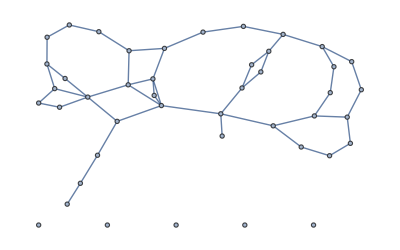

```mathematica
{mmm,ggg}=RandomSquareColoringMap[5,10,.1,.7];Print[mmm//MatrixForm];Print[ggg];
```

```mathematica
PrepareColoringLayout[option_]:=Module[{map,graph,k},
Switch[option,
0,{map,graph}=RandomSquareColoringMap[20,40,0,1];k=2,
1,{map,graph}=RandomSquareColoringMap[20,40,0.1,.7];k=4,
2,{map,graph}=RandomSquareColoringMap[20,40,0.2,.5];k=3,
3,{map,graph}=RandomSquareColoringMap[20,20,0.35,.25];k=3,
4,{map,graph}=RandomSquareColoringMap[10,10,0.5,0.5];k=3
];
Print[If[SatisfiableQ[ColoringSAT[graph,k]],"Colorable!","Not colorable!"]];
fsurfaceCRNorig=SurfaceMapColoringCRN[k];
fsurfaceorig=map;
fsurfacecoloringorig=MapColoringRules[k];
fsurfaceCRN=PreprocessFasterSurfaceCRN[fsurfaceCRNorig,{fsurfaceorig}];
fsurface=Convert2FasterSpace[{fsurfaceorig},fsurfaceCRN];
fsurfacecoloring=Convert2FasterColoring[ fsurfacecoloringorig,fsurfaceCRN];
fsurfacetime=0;
]
```

```mathematica
PrepareColoringLayout[2]
```

Colorable!

```mathematica
Dynamic[ArrayPlot[First[fsurface],ColorRules->fsurfacecoloring,PlotLabel->{fsurfacetime,fevents},ImageSize->800]]
```

```mathematica
haltedq=0;fevents=0;
With[{dt=10},While[haltedq==0,{{ddt,eventcount,haltedq},fsurface}=InfoRunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];fsurfacetime+=ddt;fevents+=eventcount]]
```

Are these random map problems hard for MiniSAT?  At all?  Let’s vary the vertex-size parameter p, then the edge-probability parameter q.  None of these seem at all hard for MiniSAT.

```mathematica
planar3hardness20q5px=Module[{n=20,q=0.5,k=3,m,g,sat,data,trials=100},
Table[PrintTemporary[p];
data=Table[{m,g}=RandomSquareColoringMap[n,n,p,q];sat=ColoringSAT[g,k];Timing[SatisfiableQ[sat]],trials];
{p,Around[#,Sqrt[#(1-#)/trials]]&@N[Count[Last/@data,True]/trials],Around[Mean[First/@data],StandardDeviation[First/@data]/Sqrt[trials]]},
{p,0,0.5,0.02}]
];
```

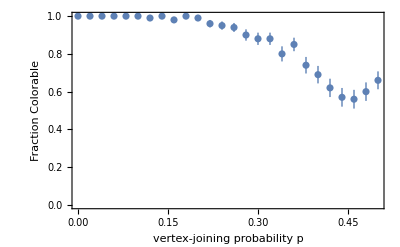
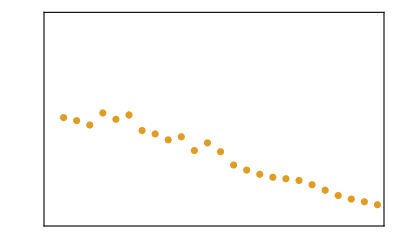

```mathematica
With[{
plot1=ListPlot[{#[[1]],#[[2]]}&/@planar3hardness20q5px,ImageSize->400,ImagePadding->40,PlotRange->{0,1},PlotStyle->ColorData[97][1],Frame->{True,True,True,False},FrameStyle->{Automatic,ColorData[97][1],Automatic,Automatic},FrameLabel->{{"Fraction Colorable",None},{"vertex-joining probability p","edge probability q=0.5"}}],
plot2=ListPlot[{#[[1]],1000#[[3]]}&/@planar3hardness20q5px,ImageSize->400,ImagePadding->40,PlotRange->{0,10},PlotStyle->ColorData[97][2],Frame->{False,False,False,True},FrameStyle->{Automatic,Automatic,Automatic,ColorData[97][2]},FrameTicks->{{False,All},{False,False}},FrameLabel->{{None,"MiniSAT time (msec)"},{None,None}}]
},Overlay[{plot1,plot2}]]
```

```mathematica
planar3hardness20p3qx=Module[{n=20,p=0.3,k=3,m,g,sat,data,trials=100},
Table[PrintTemporary[q];
data=Table[{m,g}=RandomSquareColoringMap[n,n,p,q];sat=ColoringSAT[g,k];Timing[SatisfiableQ[sat]],trials];
{q,Around[#,Sqrt[#(1-#)/trials]]&@N[Count[Last/@data,True]/trials],Around[Mean[First/@data],StandardDeviation[First/@data]/Sqrt[trials]]},
{q,0,1,0.04}]
];
```

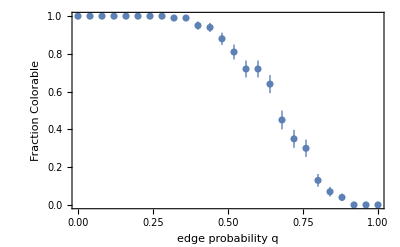
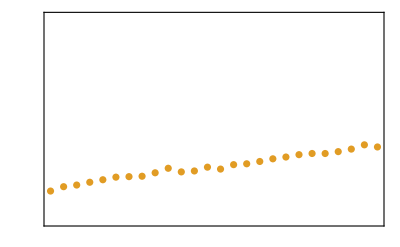

```mathematica
With[{
plot1=ListPlot[{#[[1]],#[[2]]}&/@planar3hardness20p3qx,ImageSize->400,ImagePadding->40,PlotRange->{0,1},PlotStyle->ColorData[97][1],Frame->{True,True,True,False},FrameStyle->{Automatic,ColorData[97][1],Automatic,Automatic},FrameLabel->{{"Fraction Colorable",None},{"edge probability q","vertex-joining probability p=0.3"}}],
plot2=ListPlot[{#[[1]],1000#[[3]]}&/@planar3hardness20p3qx,ImageSize->400,ImagePadding->40,PlotRange->{0,10},PlotStyle->ColorData[97][2],Frame->{False,False,False,True},FrameStyle->{Automatic,Automatic,Automatic,ColorData[97][2]},FrameTicks->{{False,All},{False,False}},FrameLabel->{{None,"MiniSAT time (msec)"},{None,None}}]
},Overlay[{plot1,plot2}]]
```

```mathematica
planar3hardness40p3qx=Module[{n=40,p=0.3,k=3,m,g,sat,data,trials=100},
Table[PrintTemporary[q];
data=Table[{m,g}=RandomSquareColoringMap[n,n,p,q];sat=ColoringSAT[g,k];Timing[SatisfiableQ[sat]],trials];
{q,Around[#,Sqrt[#(1-#)/trials]]&@N[Count[Last/@data,True]/trials],Around[Mean[First/@data],StandardDeviation[First/@data]/Sqrt[trials]]},
{q,0,1,0.04}]
];
```

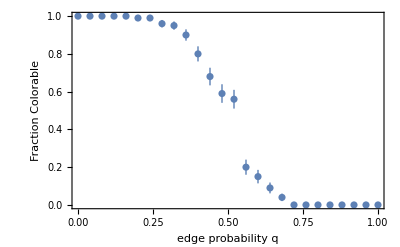
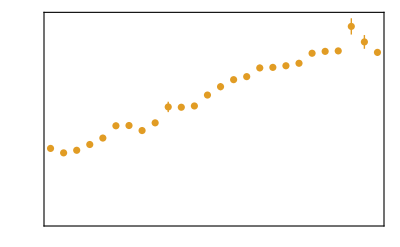

```mathematica
With[{
plot1=ListPlot[{#[[1]],#[[2]]}&/@planar3hardness40p3qx,ImageSize->400,ImagePadding->40,PlotRange->{0,1},PlotStyle->ColorData[97][1],Frame->{True,True,True,False},FrameStyle->{Automatic,ColorData[97][1],Automatic,Automatic},FrameLabel->{{"Fraction Colorable",None},{"edge probability q","vertex-joining probability p=0.3"}}],
plot2=ListPlot[{#[[1]],1000#[[3]]}&/@planar3hardness40p3qx,ImageSize->400,ImagePadding->40,PlotRange->{0,20},PlotStyle->ColorData[97][2],Frame->{False,False,False,True},FrameStyle->{Automatic,Automatic,Automatic,ColorData[97][2]},FrameTicks->{{False,All},{False,False}},FrameLabel->{{None,"MiniSAT time (msec)"},{None,None}}]
},Overlay[{plot1,plot2}]]
```

Let’s a take a look at what happens when we locally disturb a valid solution.  So, run the above until a problem of your choice has been solved, and then run the code below that will save the reference solution, and plot differences from the reference solution after perturbing a given number of connected pixels.  This is actually most insightful (initially) with the trivial 2-colorable square lattice.

```mathematica
rsurface=fsurface; (* the reference solution, found above *)
background=w/.fsurfaceCRN[[-1]];
```

```mathematica
PerturbMap[size_]:=Module[{k=Max[Flatten[RevertFaster2Space[fsurface,fsurfaceCRN]]/.{v[c_]:>c,e[c_]:>c,w->0}],numrules=fsurfaceCRN[[-2]],symrules=fsurfaceCRN[[-1]],n=Length[First[fsurface]],m=Length[First[First[fsurface]]]},
fsurface=rsurface;
Do[fsurface[[1,i,j]]=Which[
Head[fsurface[[1,i,j]]/.numrules]===v,v[RandomInteger[{1,k}]]/.symrules,
Head[fsurface[[1,i,j]]/.numrules]===e,e[RandomInteger[{1,k}]]/.symrules,
True,w/.symrules],
{i,Max[1,Round[n/2-size/2]],Min[n,Round[n/2+size/2]]},{j,Max[1,Round[m/2-size/2]],Min[m,Round[m/2+size/2]]}
];
];
```

```mathematica
PerturbMap[20]
```

```mathematica
Dynamic[ArrayPlot[MapThread[If[#2==background,-1,If[#1==#2,0,1]]&,{First[fsurface],First[rsurface]},2],ColorRules->{0->Black,1->Red,-1->White},PlotLabel->fsurfacetime,ImageSize->800]]
```

```mathematica
haltedq=0;
With[{dt=10},While[haltedq==0,{{ddt,eventcount,haltedq},fsurface}=InfoRunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];fsurfacetime+=ddt]]
```

Now let’s look at self-healing tendencies, and see if we can quantify it.

```mathematica
(* first set up map switch option 2 above, including obtaining a reference solution and setting rsurface.  *)
perturbmap2data=Module[{data,trials=100},
Table[
PrintTemporary[size];
data=Table[ 
PerturbMap[size];
fsurfacetime=0;haltedq=0;
With[{dt=1000},While[haltedq==0,{{ddt,eventcount,haltedq},fsurface}=InfoRunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];fsurfacetime+=ddt]];
fsurfacetime,
trials];
{size,Around[Mean[data],StandardDeviation[data]/Sqrt[trials]]},
{size,1,30}]
];
```

```mathematica
perturbmap2data=perturbmap2data/.Around[a_,b_]:>Around[a,b/10]
```

{{1,0.},{2,38.37.},{3,851.455.},{4,91.42.},{5,238.116.},{6,783.300.},{7,386.153.},{8,1424.894.},{9,968.469.},{10,2113.871.},{11,1285.434.},{12,2016.654.},{13,1670.622.},{14,3.41.210^3},{15,3369.899.},{16,8.03.010^3},{17,4.61.810^3},{18,3250.489.},{19,5.01.510^3},{20,3760.584.},{21,3060.563.},{22,4095.634.},{23,7.01.710^3},{24,4520.643.},{25,7.22.810^3},{26,8.01.810^3},{27,8.21.910^3},{28,1.60.410^4},{29,6327.993.},{30,8.71.710^3}}

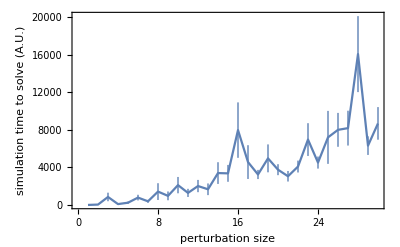

```mathematica
ListPlot[perturbmap2data,Frame->True,FrameLabel->{"perturbation size","simulation time to solve (A.U.)"},Joined->True]
```

That’s really noisy.  Maybe because either (with some probability) the size-s perturbation immediately heals, or else it expands to roughly the whole surface (or at least a decent fraction).  Maybe if we just look at the fraction that finish “real fast”, it will be a clearer message?

```mathematica
(* first set up map switch option 2 above, including obtaining a reference solution and setting rsurface.  *)
perturbmap2dataF=Module[{data,trials=100,dt=1000},
Table[
PrintTemporary[size];
data=Table[ 
PerturbMap[size];
{{ddt,eventcount,haltedq},fsurface}=InfoRunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];
haltedq,
trials];
{size,Around[Mean[data],StandardDeviation[data]/Sqrt[trials]]},
{size,1,30}]
];
```

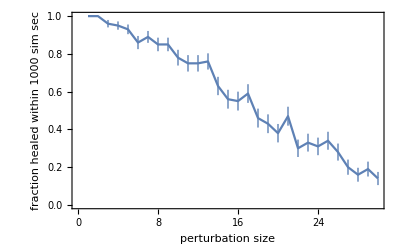

```mathematica
ListPlot[perturbmap2dataF,Frame->True,FrameLabel->{"perturbation size","fraction healed within 1000 sim sec"},Joined->True]
```

What would we like to see, if we had a “good” self-healing rule?  We’d like the time to clean up a patch to be linear in the diameter of the patch, like Toom’s rule -- but not just on average, we want a guarantee.   Yet, this conflicts with the need to explore more broadly if the context around the conflicts is not a valid solution... so I’m not sure where the desired trade-off is, in any case.

How can we modify the CRN so that it can more effectively deal with these easy cases, and maybe also the hard cases as well?  We’d like something like  WalkSATCRN (as I claimed but did not show) that exhibits a “wound healing” phenomenon .

We might ask whether Arushi’s “biasing” approach could work.  A critical consideration in the planar case is to ask about self-healing if a solution is found: will a damaged region be more likely to heal itself, or for the wound to expand?  Maybe smaller wounds are more likely to heal; if so, can we ensure that the healing is as good as possible?  In this case, if we now consider de-novo search for solutions, when the system stumbles upon a configuration that is a certain percentage correct and thus can be considered a correct solution with a few wounds, then we can expect those wounds to heal and a solution will be found.   Prior to this point, we want the system to rapidly explore configurations, but after this point, we want the system to clean up the wounds and solidify.  So, there are some connections to Ising models, Toom’s rule, Reif & Gacs, and self-healing tile sets...

Let’s find the hard-for-MiniSAT parameters of our random graph method, as well as the hard-for-SurfaceMapColoringCRN parameters.

```mathematica
MapColoringTimes[n_,m_,p_,q_,k_]:=Module[{map,graph,SATtime,CRNtime,sat,colorable=False,attempts=0,dt=1000},
While[!colorable,
{map,graph}=RandomSquareColoringMap[n,m,p,q];attempts++;
sat=ColoringSAT[graph,k];{SATtime,colorable}=AbsoluteTiming[SatisfiableQ[sat]]
];
If[attempts>10,Print["It took ",attempts," attempts to find a colorable graph!"]];
fsurfaceCRNorig=SurfaceMapColoringCRN[k];
fsurfaceorig=map;
fsurfacecoloringorig=MapColoringRules[k];
fsurfaceCRN=PreprocessFasterSurfaceCRN[fsurfaceCRNorig,{fsurfaceorig}];
fsurface=Convert2FasterSpace[{fsurfaceorig},fsurfaceCRN];
fsurfacecoloring=Convert2FasterColoring[ fsurfacecoloringorig,fsurfaceCRN];
fsurfacetime=0;haltedq=0;
{CRNtime,fsurface}=AbsoluteTiming[
While[haltedq==0,{{ddt,eventcount,haltedq},fsurface}=InfoRunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];fsurfacetime+=ddt];
fsurface
];
{attempts,VertexCount[graph],EdgeCount[graph],SATtime,CRNtime}]
```

```mathematica
MapColoringTimes[10,10,.3,.9,3]
```

{2,55,99,0.001571,18.5996}

```mathematica
mapdata10x10x3=Module[{trials=10,data},
Table[
data=Table[MapColoringTimes[10,10,p,q,3],trials];
(Print[N[#]];N[#])&@
{p,q,trials/Total[First/@data],Mean[#[[2]]&/@data],Mean[#[[3]]&/@data],Mean[#[[4]]&/@data],Mean[#[[5]]&/@data]},
{p,0,0.5,0.05},{q,0,0.9,0.1}]]
```

{0.,0.,1.,101.,0.,0.0025667,0.000636}

{0.,0.1,1.,101.,16.,0.0009641,0.0108307}

{0.,0.2,1.,101.,36.6,0.0012258,0.0255908}

{0.,0.3,1.,101.,56.2,0.0012747,0.037842}

{0.,0.4,1.,101.,74.2,0.0024964,0.0553109}

{0.,0.5,1.,101.,88.,0.0020664,0.0752213}

{0.,0.6,1.,101.,109.1,0.0017079,0.108156}

{0.,0.7,1.,101.,126.7,0.0017805,0.143416}

{0.,0.8,1.,101.,145.7,0.0020493,0.188004}

{0.,0.9,1.,101.,162.2,0.0017988,0.322331}

{0.05,0.,1.,92.2,0.,0.0008455,0.0005578}

{0.05,0.1,1.,91.1,19.,0.0008968,0.0194291}

{0.05,0.2,1.,92.8,34.6,0.0009713,0.0389026}

{0.05,0.3,1.,91.8,52.,0.0010079,0.0635045}

{0.05,0.4,1.,92.1,64.7,0.0010557,0.0688395}

{0.05,0.5,1.,92.8,83.7,0.0012339,0.0952292}

{0.05,0.6,1.,90.4,102.3,0.0012474,0.169722}

{0.05,0.7,1.,92.7,120.6,0.0013311,0.254991}

{0.05,0.8,1.,92.1,138.6,0.0014301,0.321829}

{0.05,0.9,1.,90.6,151.4,0.0014772,0.643474}

{0.1,0.,1.,81.9,0.,0.0006551,0.0005733}

{0.1,0.1,1.,82.8,15.5,0.0007325,0.0251576}

{0.1,0.2,1.,80.9,32.4,0.0007931,0.0527165}

{0.1,0.3,1.,82.9,48.2,0.0009479,0.0709025}

{0.1,0.4,1.,82.8,66.2,0.0017072,0.122706}

{0.1,0.5,1.,82.7,79.1,0.0013215,0.190746}

{0.1,0.6,1.,85.3,98.9,0.0026571,0.276028}

{0.1,0.7,1.,82.6,110.2,0.0014554,0.419306}

{0.1,0.8,1.,81.8,127.5,0.001506,0.947385}

{0.1,0.9,0.909091,84.6,145.7,0.0014448,1.77477}

{0.15,0.,1.,75.5,0.,0.000609,0.0006148}

{0.15,0.1,1.,73.1,15.7,0.0007147,0.0422415}

{0.15,0.2,1.,74.3,31.1,0.0007853,0.0757957}

{0.15,0.3,1.,74.2,45.5,0.0009623,0.105198}

{0.15,0.4,1.,72.4,61.4,0.000939,0.135959}

{0.15,0.5,1.,70.7,68.7,0.0009497,0.271615}

{0.15,0.6,1.,73.4,87.9,0.0010505,0.36018}

{0.15,0.7,1.,73.8,105.6,0.0011375,0.78073}

{0.15,0.8,1.,75.9,118.2,0.0012196,1.73762}

{0.15,0.9,1.,73.6,130.9,0.0013673,5.69468}

{0.2,0.,1.,63.9,0.,0.0013339,0.0006811}

{0.2,0.1,1.,59.9,13.,0.000664,0.0646486}

{0.2,0.2,1.,65.,26.,0.0007751,0.128395}

{0.2,0.3,1.,65.1,38.5,0.0012448,0.228207}

{0.2,0.4,1.,66.3,53.7,0.0009333,0.189396}

{0.2,0.5,1.,66.9,67.8,0.0010028,0.324769}

{0.2,0.6,1.,66.3,83.7,0.0010817,0.906254}

{0.2,0.7,1.,65.4,90.2,0.0012946,1.22533}

{0.2,0.8,1.,64.3,100.8,0.0012043,1.45823}

{0.2,0.9,0.909091,64.5,114.9,0.0012653,25.6027}

{0.25,0.,1.,56.1,0.,0.0005896,0.0006329}

{0.25,0.1,1.,57.7,11.6,0.0022551,0.0785766}

{0.25,0.2,1.,54.,23.4,0.0006476,0.153188}

{0.25,0.3,1.,56.5,37.8,0.0008698,0.260972}

{0.25,0.4,1.,55.9,49.3,0.0008261,0.398926}

{0.25,0.5,1.,55.5,60.6,0.0008533,0.448152}

{0.25,0.6,1.,58.3,72.3,0.001605,1.3449}

{0.25,0.7,0.909091,57.7,82.4,0.0010829,1.3534}

{0.25,0.8,0.714286,58.5,94.4,0.0010205,3.60985}

{0.25,0.9,0.5,59.4,107.5,0.0011368,33.3507}

{0.3,0.,1.,48.8,0.,0.0006095,0.0006534}

{0.3,0.1,1.,49.,12.1,0.0005099,0.191585}

{0.3,0.2,1.,48.2,23.6,0.0005701,0.169647}

{0.3,0.3,1.,52.4,37.5,0.0006406,0.365927}

{0.3,0.4,1.,50.,44.5,0.0006399,0.582399}

{0.3,0.5,1.,48.,52.5,0.0006782,1.05845}

{0.3,0.6,0.909091,47.6,61.,0.0007617,1.1857}

{0.3,0.7,0.833333,45.5,66.6,0.0007979,5.42341}

{0.3,0.8,0.666667,47.5,77.4,0.0008446,6.77214}

{0.3,0.9,0.5,49.3,89.,0.0016126,18.6009}

{0.35,0.,1.,40.1,0.,0.0004633,0.0006589}

{0.35,0.1,1.,36.5,10.4,0.0004068,0.259965}

{0.35,0.2,1.,39.4,19.3,0.0005157,0.418954}

{0.35,0.3,1.,43.3,32.1,0.0005985,0.430435}

{0.35,0.4,1.,42.,38.9,0.0006329,0.941725}

{0.35,0.5,1.,39.2,45.5,0.0006416,1.43751}

{0.35,0.6,0.833333,37.9,50.,0.0007155,2.77631}

{0.35,0.7,0.909091,39.3,58.8,0.0007575,5.44419}

{0.35,0.8,0.769231,44.5,71.9,0.0008208,4.227}

{0.35,0.9,0.4,38.3,68.,0.0007576,27.5086}

{0.4,0.,1.,29.8,0.,0.000307,0.0005695}

{0.4,0.1,1.,28.2,7.3,0.0003154,0.373858}

{0.4,0.2,1.,28.5,17.9,0.0003619,0.862}

{0.4,0.3,1.,31.7,23.9,0.0004253,1.62563}

{0.4,0.4,0.833333,31.8,29.9,0.0004232,0.761986}

{0.4,0.5,0.909091,30.3,34.4,0.0004582,2.55558}

{0.4,0.6,0.833333,26.5,34.1,0.0004531,1.90262}

{0.4,0.7,0.833333,33.2,47.,0.0005982,4.17715}

{0.4,0.8,0.526316,29.9,48.4,0.0006651,6.39578}

{0.4,0.9,0.454545,33.6,59.2,0.0006532,29.9668}

{0.45,0.,1.,23.8,0.,0.0002316,0.0005461}

{0.45,0.1,1.,27.2,6.5,0.0002989,0.776801}

{0.45,0.2,1.,24.7,14.9,0.0003304,1.61956}

{0.45,0.3,1.,26.3,20.3,0.0003515,1.11139}

{0.45,0.4,0.909091,26.,25.,0.0003799,2.25026}

{0.45,0.5,0.833333,23.1,26.1,0.0003549,1.76077}

{0.45,0.6,0.833333,21.9,28.4,0.0003586,4.2554}

{0.45,0.7,0.666667,25.3,36.,0.0004205,2.83224}

{0.45,0.8,0.769231,22.1,32.9,0.0003767,7.09091}

{0.45,0.9,0.344828,24.4,39.5,0.0004487,13.4064}

{0.5,0.,1.,18.6,0.,0.0001849,0.0005293}

{0.5,0.1,1.,17.9,4.4,0.0002081,0.883601}

{0.5,0.2,1.,18.4,10.3,0.0002428,1.49167}

{0.5,0.3,1.,17.6,13.7,0.0002623,2.52272}

{0.5,0.4,1.,18.3,18.1,0.0002911,1.98074}

{0.5,0.5,1.,19.2,20.5,0.0003113,2.51648}

{0.5,0.6,0.625,17.5,22.2,0.0003008,4.68589}

{0.5,0.7,0.909091,15.5,18.9,0.0002996,2.78962}

{0.5,0.8,0.666667,18.3,25.7,0.0003415,3.67664}

{0.5,0.9,0.47619,15.7,21.,0.0002699,2.78269}

{{{0.,0.,1.,101.,0.,0.0025667,0.000636},{0.,0.1,1.,101.,16.,0.0009641,0.0108307},{0.,0.2,1.,101.,36.6,0.0012258,0.0255908},{0.,0.3,1.,101.,56.2,0.0012747,0.037842},{0.,0.4,1.,101.,74.2,0.0024964,0.0553109},{0.,0.5,1.,101.,88.,0.0020664,0.0752213},{0.,0.6,1.,101.,109.1,0.0017079,0.108156},{0.,0.7,1.,101.,126.7,0.0017805,0.143416},{0.,0.8,1.,101.,145.7,0.0020493,0.188004},{0.,0.9,1.,101.,162.2,0.0017988,0.322331}},{{0.05,0.,1.,92.2,0.,0.0008455,0.0005578},{0.05,0.1,1.,91.1,19.,0.0008968,0.0194291},{0.05,0.2,1.,92.8,34.6,0.0009713,0.0389026},{0.05,0.3,1.,91.8,52.,0.0010079,0.0635045},{0.05,0.4,1.,92.1,64.7,0.0010557,0.0688395},{0.05,0.5,1.,92.8,83.7,0.0012339,0.0952292},{0.05,0.6,1.,90.4,102.3,0.0012474,0.169722},{0.05,0.7,1.,92.7,120.6,0.0013311,0.254991},{0.05,0.8,1.,92.1,138.6,0.0014301,0.321829},{0.05,0.9,1.,90.6,151.4,0.0014772,0.643474}},{{0.1,0.,1.,81.9,0.,0.0006551,0.0005733},{0.1,0.1,1.,82.8,15.5,0.0007325,0.0251576},{0.1,0.2,1.,80.9,32.4,0.0007931,0.0527165},{0.1,0.3,1.,82.9,48.2,0.0009479,0.0709025},{0.1,0.4,1.,82.8,66.2,0.0017072,0.122706},{0.1,0.5,1.,82.7,79.1,0.0013215,0.190746},{0.1,0.6,1.,85.3,98.9,0.0026571,0.276028},{0.1,0.7,1.,82.6,110.2,0.0014554,0.419306},{0.1,0.8,1.,81.8,127.5,0.001506,0.947385},{0.1,0.9,0.909091,84.6,145.7,0.0014448,1.77477}},{{0.15,0.,1.,75.5,0.,0.000609,0.0006148},{0.15,0.1,1.,73.1,15.7,0.0007147,0.0422415},{0.15,0.2,1.,74.3,31.1,0.0007853,0.0757957},{0.15,0.3,1.,74.2,45.5,0.0009623,0.105198},{0.15,0.4,1.,72.4,61.4,0.000939,0.135959},{0.15,0.5,1.,70.7,68.7,0.0009497,0.271615},{0.15,0.6,1.,73.4,87.9,0.0010505,0.36018},{0.15,0.7,1.,73.8,105.6,0.0011375,0.78073},{0.15,0.8,1.,75.9,118.2,0.0012196,1.73762},{0.15,0.9,1.,73.6,130.9,0.0013673,5.69468}},{{0.2,0.,1.,63.9,0.,0.0013339,0.0006811},{0.2,0.1,1.,59.9,13.,0.000664,0.0646486},{0.2,0.2,1.,65.,26.,0.0007751,0.128395},{0.2,0.3,1.,65.1,38.5,0.0012448,0.228207},{0.2,0.4,1.,66.3,53.7,0.0009333,0.189396},{0.2,0.5,1.,66.9,67.8,0.0010028,0.324769},{0.2,0.6,1.,66.3,83.7,0.0010817,0.906254},{0.2,0.7,1.,65.4,90.2,0.0012946,1.22533},{0.2,0.8,1.,64.3,100.8,0.0012043,1.45823},{0.2,0.9,0.909091,64.5,114.9,0.0012653,25.6027}},{{0.25,0.,1.,56.1,0.,0.0005896,0.0006329},{0.25,0.1,1.,57.7,11.6,0.0022551,0.0785766},{0.25,0.2,1.,54.,23.4,0.0006476,0.153188},{0.25,0.3,1.,56.5,37.8,0.0008698,0.260972},{0.25,0.4,1.,55.9,49.3,0.0008261,0.398926},{0.25,0.5,1.,55.5,60.6,0.0008533,0.448152},{0.25,0.6,1.,58.3,72.3,0.001605,1.3449},{0.25,0.7,0.909091,57.7,82.4,0.0010829,1.3534},{0.25,0.8,0.714286,58.5,94.4,0.0010205,3.60985},{0.25,0.9,0.5,59.4,107.5,0.0011368,33.3507}},{{0.3,0.,1.,48.8,0.,0.0006095,0.0006534},{0.3,0.1,1.,49.,12.1,0.0005099,0.191585},{0.3,0.2,1.,48.2,23.6,0.0005701,0.169647},{0.3,0.3,1.,52.4,37.5,0.0006406,0.365927},{0.3,0.4,1.,50.,44.5,0.0006399,0.582399},{0.3,0.5,1.,48.,52.5,0.0006782,1.05845},{0.3,0.6,0.909091,47.6,61.,0.0007617,1.1857},{0.3,0.7,0.833333,45.5,66.6,0.0007979,5.42341},{0.3,0.8,0.666667,47.5,77.4,0.0008446,6.77214},{0.3,0.9,0.5,49.3,89.,0.0016126,18.6009}},{{0.35,0.,1.,40.1,0.,0.0004633,0.0006589},{0.35,0.1,1.,36.5,10.4,0.0004068,0.259965},{0.35,0.2,1.,39.4,19.3,0.0005157,0.418954},{0.35,0.3,1.,43.3,32.1,0.0005985,0.430435},{0.35,0.4,1.,42.,38.9,0.0006329,0.941725},{0.35,0.5,1.,39.2,45.5,0.0006416,1.43751},{0.35,0.6,0.833333,37.9,50.,0.0007155,2.77631},{0.35,0.7,0.909091,39.3,58.8,0.0007575,5.44419},{0.35,0.8,0.769231,44.5,71.9,0.0008208,4.227},{0.35,0.9,0.4,38.3,68.,0.0007576,27.5086}},{{0.4,0.,1.,29.8,0.,0.000307,0.0005695},{0.4,0.1,1.,28.2,7.3,0.0003154,0.373858},{0.4,0.2,1.,28.5,17.9,0.0003619,0.862},{0.4,0.3,1.,31.7,23.9,0.0004253,1.62563},{0.4,0.4,0.833333,31.8,29.9,0.0004232,0.761986},{0.4,0.5,0.909091,30.3,34.4,0.0004582,2.55558},{0.4,0.6,0.833333,26.5,34.1,0.0004531,1.90262},{0.4,0.7,0.833333,33.2,47.,0.0005982,4.17715},{0.4,0.8,0.526316,29.9,48.4,0.0006651,6.39578},{0.4,0.9,0.454545,33.6,59.2,0.0006532,29.9668}},{{0.45,0.,1.,23.8,0.,0.0002316,0.0005461},{0.45,0.1,1.,27.2,6.5,0.0002989,0.776801},{0.45,0.2,1.,24.7,14.9,0.0003304,1.61956},{0.45,0.3,1.,26.3,20.3,0.0003515,1.11139},{0.45,0.4,0.909091,26.,25.,0.0003799,2.25026},{0.45,0.5,0.833333,23.1,26.1,0.0003549,1.76077},{0.45,0.6,0.833333,21.9,28.4,0.0003586,4.2554},{0.45,0.7,0.666667,25.3,36.,0.0004205,2.83224},{0.45,0.8,0.769231,22.1,32.9,0.0003767,7.09091},{0.45,0.9,0.344828,24.4,39.5,0.0004487,13.4064}},{{0.5,0.,1.,18.6,0.,0.0001849,0.0005293},{0.5,0.1,1.,17.9,4.4,0.0002081,0.883601},{0.5,0.2,1.,18.4,10.3,0.0002428,1.49167},{0.5,0.3,1.,17.6,13.7,0.0002623,2.52272},{0.5,0.4,1.,18.3,18.1,0.0002911,1.98074},{0.5,0.5,1.,19.2,20.5,0.0003113,2.51648},{0.5,0.6,0.625,17.5,22.2,0.0003008,4.68589},{0.5,0.7,0.909091,15.5,18.9,0.0002996,2.78962},{0.5,0.8,0.666667,18.3,25.7,0.0003415,3.67664},{0.5,0.9,0.47619,15.7,21.,0.0002699,2.78269}}}

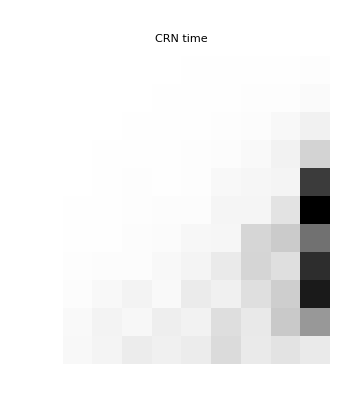

```mathematica
ArrayPlot[Map[Last,mapdata10x10x3,{2}],PlotLabel->"CRN time",FrameTicks->Automatic,FrameLabel->{"region-joining probability p (index)","edge probability q (index)"}]
```

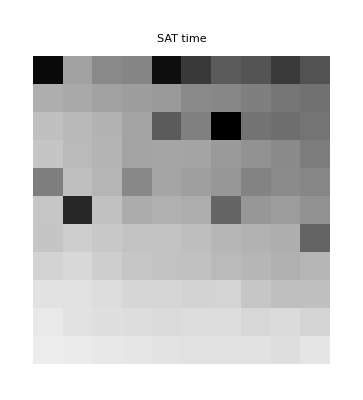

```mathematica
ArrayPlot[Map[#[[-2]]&,mapdata10x10x3,{2}],PlotLabel->"SAT time",FrameTicks->Automatic,FrameLabel->{"region-joining probability p (index)","edge probability q (index)"}]
```

```mathematica
ListPlot3D[#[[{1,2,7}]]&/@Flatten[mapdata10x10x3,1],PlotLabel->"CRN time",AxesLabel->{"region-joining probability p","edge probability q"},PlotRange->All,ImageSize->1000]
```

-Graphics3D-

```mathematica
First[Sort[Flatten[mapdata10x10x3,1],Last[#1]>Last[#2]&]]
```

{0.25,0.9,0.5,59.4,107.5,0.0011368,33.3507}

## Back to the basics: the Ising model is like a 2-color planar lattice graph coloring problem.

Here’s the Ising model.  Asynchronous updates.  0/1 states.  Energy function based on sum coupling between like or dislike states:  E=∑_(i,j) If[x_i= x_j, w_(i,j),-w_(i,j)] where w_(i,j)=If[ i and j are neighbors,coupling, 0].  Updates satisfy detailed balance in the discrete-time Markov chain.  The coupling energy could be thought of as some G/k T where a large positive number implies neighboring sites are penalized for being the same (anti-ferromagnetic) while a large negative number implies neighboring sites are stabilized by being the same (ferromagnetic).

Thus, the antiferromagnetic case is like 2-coloring a lattice.    But the dynamics are isomorphic in those two cases -- the ferromagnetic case is more pleasant to watch.

```mathematica
RunIsing=Compile[{{space,_Integer,3},{coupling,_Real},{rounds,_Real}},
Module[{S=space,dims=Dimensions[space],l,m,n,i,j,k,count,neighbors,di,dj,dk,dE,r,s},
{l,m,n}=dims;neighbors={{+1,0,0},{-1,0,0},{0,+1,0},{0,-1,0},{0,0,+1},{0,0,-1}};
Do[
i=RandomInteger[{1,l}];j=RandomInteger[{1,m}];k=RandomInteger[{1,n}];count={0,0};
Do[{di,dj,dk}=neighbors[[r]];If[1≤i+di≤l&&1≤j+dj≤m&&1≤k+dk≤n,count[[1+S[[i+di,j+dj,k+dk]]]]++],{r,1,6}];
dE=coupling * (count[[1]]-count[[2]]);
S[[i,j,k]]=If[RandomReal[]<Exp[-dE]/(1+Exp[-dE]),0,1],
{s,Round[l*m*n*rounds]}];
S
]]
```

```mathematica
Dynamic[ArrayPlot[First[ising],ColorRules->{0->Black,1->White}]]
```

```mathematica
(* random 2D initial conditions *)
ising=RandomChoice[{0,1},{1,100,100}];While[True,ising=RunIsing[ising,-10,1.0]]
```

```mathematica
(* 20x20 island in 2D sea *)
ising={ArrayPad[Table[1,30,30],100,0]};isingsize=Length[Flatten[ising]];
While[With[{tot=Total[Flatten[ising]]},tot*(isingsize-tot)≠0],ising=RunIsing[ising,-10,1.0]]
```

```mathematica
Dynamic[Show[
Graphics3D[{Black,Point/@Tuples[Transpose[{{0,0,0},Reverse[Dimensions[ising]]}]]}],
ArrayPlot3D[ising]
]]
```

```mathematica
(* random3D initial conditions *)
ising=RandomChoice[{0,1},{30,30,30}];While[True,ising=RunIsing[ising,-10,1.0]]
```

```mathematica
(* 20x20x20 island in 3D sea *)
ising=ArrayPad[Table[1,20,20,20],20,0];isingsize=Length[Flatten[ising]];
While[With[{tot=Total[Flatten[ising]]},tot*(isingsize-tot)≠0],ising=RunIsing[ising,-10,1.0]]
```

There are two phenomena to consider.   The first is how long it takes to stabilize a random initial conditions, which we could call “searching” for a solution.  The second is how long it takes to clear up an island of disagreement withing a sea of correctness, which we could call “self-healing”.    If self-healing is strong, then once search gets close enough to a solution, it will zoom in on it.   But if self-healing is too strong, it may stabilize a locally-correct solution that can’t be extended to a full solution, or it may simply locally stabilize two incompatible solutions and make it harder for one of them to win -- in both cases, impeding the search.

```mathematica
ising1dtimes=Module[{space=300,island=20,dt=1,time,trials=50,times},Table[
PrintTemporary["Starting island size ",i];
times=Table[
ising={{ArrayPad[Table[1,i],space,0]}};isingsize=Length[Flatten[ising]];time=0;
While[With[{tot=Total[Flatten[ising]]},tot*(isingsize-tot)≠0],ising=RunIsing[ising,-10,dt];time+=dt];
time,
trials];
{i,Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]},
{i,1,island}]];
```

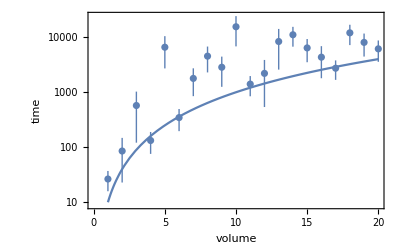

```mathematica
Show[ListLogPlot[ising1dtimes,Frame->True,FrameLabel->{"volume","time"}],LogPlot[10 n^2,{n,1,20}]]
```

```mathematica
ising2dtimes=Module[{space=30,island=100,dt=1,time,trials=50,times},Table[
PrintTemporary["Starting island size ",i];
times=Table[
ising={ArrayPad[ArrayReshape[Table[1,i],{Ceiling[Sqrt[i]],Ceiling[Sqrt[i]]},0],space,0]};
isingsize=Length[Flatten[ising]];time=0;
While[With[{tot=Total[Flatten[ising]]},tot*(isingsize-tot)≠0],ising=RunIsing[ising,-10,dt];time+=dt];
time,
trials];
{i,Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]},
{i,1,island}]];
```

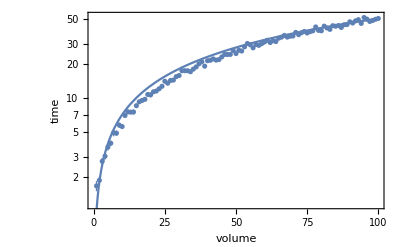

```mathematica
Show[ListLogPlot[ising2dtimes,Frame->True,FrameLabel->{"volume","time"}],LogPlot[n^0.85,{n,1,100}]]
```

```mathematica
ising3dtimes=Module[{space=10,island=100,dt=1,time,trials=50,times},Table[
PrintTemporary["Starting island size ",i];
times=Table[
ising=ArrayPad[ArrayReshape[Table[1,i],{Ceiling[i^(1/3)],Ceiling[i^(1/3)],Ceiling[i^(1/3)]},0],space,0];
isingsize=Length[Flatten[ising]];time=0;
While[With[{tot=Total[Flatten[ising]]},tot*(isingsize-tot)≠0],ising=RunIsing[ising,-10,dt];time+=dt];
time,
trials];
{i,Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]},
{i,1,island}]];
```

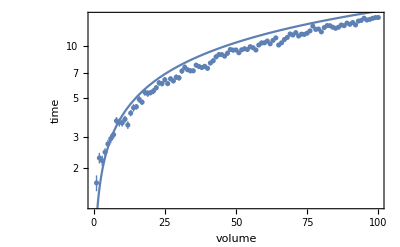

```mathematica
Show[ListLogPlot[ising3dtimes,Frame->True,FrameLabel->{"volume","time"}],LogPlot[n^0.6,{n,1,100}]]
```

The Ising model is well-studied.  Here we are interested in the low-temperature limit with Metropolis DTMC dynamics.  At zero-temperature (and coupling = -10 is a good approximation of that) we only allow moves that maintain the number of neighbor mismatches or decrease them.

The time to clear an island of n 1’s in a sea of 0’s is the time for a 1D unbiased random walk to hit the origin starting at n. Turns out (in an infinite sea) the expected time is infinite, even though the probability to eventually return is 1.   So the 1D runtime curve above is entirely an “artifact” of the limited size of the space and the limited number of trials.   If we had started withn 1’s next to n 0’s, i.e. a space of size 2n, then the time to hit either all-0 or all-1 would be O(n^2).   I am not sure what to make of the actual results from our simulations here; with enough trials, we would have occasionally encountered super-slow runs (and/or runs that flip the entire space), increasing the mean time regardless of n. 

In 2D, a region of 1’s in a sea of 0’s will never be able to exceed the initial bounding box (at temperature zero).  We can think of each side of the box doing an unbiased random walk until in the last step, one layer of pixels disappears and the bounding box irreversibly shrinks.  Let’s say the bounding box has sides of length r.  I would expect the time for one side to shrink to zero would be O(r^2).   So a naive estimation would be that to shrink all the way to zero, the expected time would be O(∑_(i=1)^r i^2)=O(r^3)=O(n^(3/2)) where n=r^2 is the number of pixels to be cleared.  Yet that’s not the exponent that we see, empirically.

The 3D case also results in monotonic shrinkage of the bounding cube, as well as monotonic shrinkage of the bounding box of facet layers.  Our naive argument would now require O(∑_(i=1)^r i^3)=O(r^4)=O(n^(4/3)) where n=r^3.   Again, the errors seem to clear even faster.   Maybe it’s because the stages are not strictly sequential, but are occurring to a large degree in parallel?

Definitely worth scouring the literature to find some analysis of this... but regardless, fast clearance of the inconsistent regions is good.

That said, it is notable that starting from random initial conditions rather than islands will consistently resolve to a weird topologically trapped configuration for coupling = -10, but will fairly frequently resolve to a uniform state for coupling = -1.

## Back to the basics: a surface CRN related (somewhat) to the Ising model

A simple surface CRN is quite similar. Try in 1D, 2D, 3D.  Note the difference: Ising strongly prefers to change a site to a color consistent with as many neighbors as possible; the surface CRN just changes when there is a disagreement, but in an arbitrary way (like Petford & Welsh’s “voter” system).  Actually, the dynamics are quite different, and it’s worth thinking about it more.  (The Naive Droplet CRN would match, on the other hand, and like the Ising model shares something with Petford & Welsh’s exponentially-weighted version.)

First we watch it, then we quantify how long it takes for an island of wrong to be rectified.

```mathematica
IsingCRN={rxn[X+Y,X+X,1],rxn[X+Y,Y+Y,1]};
IsingRandomSurface1D[n_]:={{Table[RandomChoice[{X,Y}],n]}}
IsingRandomSurface2D[n_]:={Table[RandomChoice[{X,Y}],n,n]}
IsingRandomSurface3D[n_]:=Table[RandomChoice[{X,Y}],n,n,n]
IsingIslandSurface1D[i_,space_]:={{Table[X,space]~Join~Table[Y,i]~Join~Table[X,space]}}
IsingIslandSurface2D[i_,space_]:={ArrayPad[ArrayReshape[Table[Y,i],{Ceiling[Sqrt[i]],Ceiling[Sqrt[i]]},X],space,X]}
IsingIslandSurface3D[i_,space_]:=ArrayPad[ArrayReshape[Table[Y,i],{Ceiling[i^(1/3)],Ceiling[i^(1/3)],Ceiling[i^(1/3)]},X],space,X]
IsingColoring={X->Black,Y->White};
```

```mathematica
(* we'll use global variables *)
RunIsingSurface[surface_,dt_,pause_:0]:=Module[{},
surfaceCRN=IsingCRN;
surfacecoloring=IsingColoring/.If[Length[surface]>1,{Black->Empty},{}];
fsurfaceCRN=PreprocessFasterSurfaceCRN[surfaceCRN,surface];
fsurface=Convert2FasterSpace[surface,fsurfaceCRN];
fsurfacecoloring=Convert2FasterColoring[surfacecoloring,fsurfaceCRN]; 
fsurfacetime=0;haltedq=0;
While[haltedq==0,Pause[pause];{{ddt,eventcount,haltedq},fsurface}=InfoRunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];fsurfacetime+=ddt];
]
```

```mathematica
Dynamic[If[Length[fsurface]==1,
ArrayPlot[First[fsurface],ColorRules->fsurfacecoloring,PlotLabel->fsurfacetime,ImageSize->Large], (* for 1D and 2D *)
ShowSurface3D[fsurface,fsurfacecoloring,PlotLabel->fsurfacetime] (* for 3D *)
]]
```

```mathematica
RunIsingSurface[IsingRandomSurface1D[300],1.0,0.1]
```

```mathematica
RunIsingSurface[IsingIslandSurface1D[20,300],1.0,0.1]
```

```mathematica
RunIsingSurface[IsingRandomSurface2D[100],1.0]
```

```mathematica
RunIsingSurface[IsingIslandSurface2D[30,100],1.0]
```

```mathematica
RunIsingSurface[IsingRandomSurface3D[20],1.0]
```

```mathematica
RunIsingSurface[IsingIslandSurface3D[20,20],1.0]
```

Now look at the scaling for cleaning up an island of imperfection.

```mathematica
isingsurface1dtimes=Module[{space=300,island=30,dt=100,trials=400,times},Table[
PrintTemporary["Starting island size ",i];
times=Table[RunIsingSurface[IsingIslandSurface1D[i,space],dt];fsurfacetime,trials];
{i,Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]},
{i,1,island}]];
```

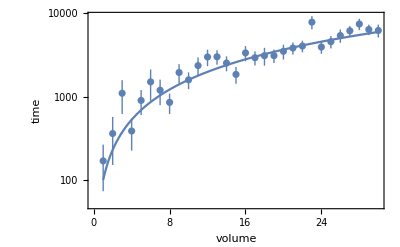

```mathematica
Show[ListLogPlot[isingsurface1dtimes,Frame->True,FrameLabel->{"volume","time"}],LogPlot[100n^1.2,{n,1,30}]]
```

As for the Ising model, in 1D we have an unbiased random walk that, in the limit of a large space, will have infinite expected clearance time -- and thus the distribution of runtimes has very long tails.  So the results here somehow reflect the number of trials (i.e. how often we hit the long tails) and the size of the space (i.e. how often the random walk hits the walls).    Incidentally: the simulations here are a lot faster than the Ising model simulations, because the Ising simulator continually updates all cells regardless of whether they are likely to change or not, while the surface CRN simulator only updates sites where a reaction is possible -- which for these 1D simulations will just be the two places where the color changes.

```mathematica
isingsurface2dtimes=Module[{space=250,island=20,dt=100,trials=30,times},Table[
PrintTemporary["Starting island size ",i];
times=Table[RunIsingSurface[IsingIslandSurface2D[i,space],dt];fsurfacetime,trials];
{i,Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]},
{i,1,island}]];
```

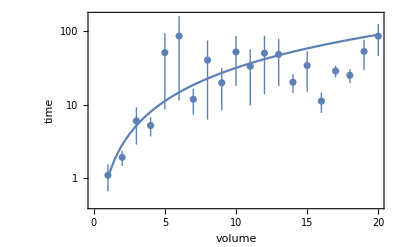

```mathematica
Show[ListLogPlot[isingsurface2dtimes,Frame->True,FrameLabel->{"volume","time"}],LogPlot[n^1.5,{n,1,20}]]
```

This is truly way more terrible than I expected.  Very long-tailed, and quite unlike the Ising model.  Decent probability that a tiny error will expand into a conflagration.   Especially problematic if the conflagration hits the wall, whereupon it becomes harder to shrink (since we don’t have wrap-around).  If you don’t do too many trials, you might get lucky and avoid the really bad conflagrations.   So I repeated with fewer trials until the run succeeded.  Thus this data is already suspect, due to selection bias.  Nonetheless, I expected the Ising model self-healing time to go as r^3 and here n=r^2 so in that case we’d have time scaling with n^(3/2), and that fits OK here despite that the argument fails to match the actual Ising model data.  Also, the noise is too much to believe the results here, given the long tails concern.

```mathematica
isingsurface3dtimes=Module[{space=30,island=20,dt=100,trials=50,times},Table[
PrintTemporary["Starting island size ",i];
times=Table[RunIsingSurface[IsingIslandSurface3D[i,space],dt];fsurfacetime,trials];
{i,Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]},
{i,1,island}]];
```

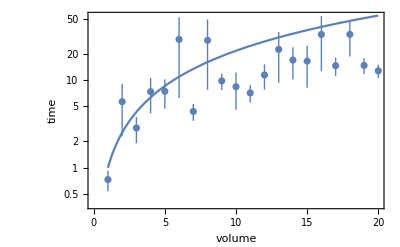

```mathematica
Show[ListLogPlot[isingsurface3dtimes,Frame->True,FrameLabel->{"volume","time"}],LogPlot[n^(4/3),{n,1,20}]]
```

Long tails again!  Still, we can say that the higher the dimensionality, the faster the errors are cleared up.

Bottom line: These three cases (1D, 2D, 3D) provide “simple” base cases (2 colors) on which we can evaluate a surface CRN K-coloring algorithm -- before worrying about complicated graphs, we might want our algorithm to give good performance on these cases.  (However, it doesn’t make sense to design an algorithm specifically with only these test cases in mind, since the 1D, 2D, and 3D rectilinear lattices are all 2-colorable -- being able to solve them well means nothing in and of itself.)

Future:  

Include Toom’s rule among the examples here.  How might Toom’s rule generalize to arbitrary graphs and K colors?

Does the well-mixed fast majority CRN translate into an effective surface CRN for 2 (or more?) colors?  { B + W --> U + U, U + B --> B + B, U + W --> W + W }   I imagine that for 1D it’s no better, but perhaps it’s an improvement for 2D and 3D?

Can we design a surface CRN that provides a directional “sweep” sort of like Toom’s rule, or perhaps sort of like Greenberg-Hastings?

```mathematica
MajorityCRN={rxn[X+Y,U+U,1],rxn[U+Y,Y+Y,1],rxn[U+X,X+X,1]};
MajorityRandomSurface1D[n_]:={{Table[RandomChoice[{X,Y}],n]}}
MajorityRandomSurface2D[n_]:={Table[RandomChoice[{X,Y}],n,n]}
MajorityRandomSurface3D[n_]:=Table[RandomChoice[{X,Y}],n,n,n]
MajorityIslandSurface1D[i_,space_]:={{Table[X,space]~Join~Table[Y,i]~Join~Table[X,space]}}
MajorityIslandSurface2D[i_,space_]:={ArrayPad[ArrayReshape[Table[Y,i],{Ceiling[Sqrt[i]],Ceiling[Sqrt[i]]},X],space,X]}
MajorityIslandSurface3D[i_,space_]:=ArrayPad[ArrayReshape[Table[Y,i],{Ceiling[i^(1/3)],Ceiling[i^(1/3)],Ceiling[i^(1/3)]},X],space,X]
MajorityColoring={X->Black,Y->White,U->Red};
```

```mathematica
(* we'll use global variables *)
RunMajoritySurface[surface_,dt_,pause_:0]:=Module[{},
surfaceCRN=MajorityCRN;
surfacecoloring=MajorityColoring/.If[Length[surface]>1,{Black->Empty},{}];
fsurfaceCRN=PreprocessFasterSurfaceCRN[surfaceCRN,surface];
fsurface=Convert2FasterSpace[surface,fsurfaceCRN];
fsurfacecoloring=Convert2FasterColoring[surfacecoloring,fsurfaceCRN]; 
fsurfacetime=0;haltedq=0;
While[haltedq==0,Pause[pause];{{ddt,eventcount,haltedq},fsurface}=InfoRunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];fsurfacetime+=ddt];
]
```

```mathematica
Dynamic[If[Length[fsurface]==1,
ArrayPlot[First[fsurface],ColorRules->fsurfacecoloring,PlotLabel->fsurfacetime,ImageSize->Large], (* for 1D and 2D *)
ShowSurface3D[fsurface,fsurfacecoloring,PlotLabel->fsurfacetime] (* for 3D *)
]]
```

```mathematica
RunMajoritySurface[MajorityRandomSurface1D[300],1.0,0.1]
```

```mathematica
RunMajoritySurface[MajorityIslandSurface1D[20,300],1.0,0.1]
```

```mathematica
RunMajoritySurface[MajorityRandomSurface2D[200],1.0]
```

```mathematica
RunMajoritySurface[MajorityIslandSurface2D[30,100],1.0]
```

```mathematica
RunMajoritySurface[MajorityRandomSurface3D[20],1.0]
```

```mathematica
RunMajoritySurface[MajorityIslandSurface3D[20,20],1.0]
```

That looks surprising good (except for 1D, which is the same old same old).  Let’s quantify:

```mathematica
majoritysurface2dtimes=Module[{space=250,island=100,dt=100,trials=50,times},Table[
PrintTemporary["Starting island size ",i];
times=Table[RunMajoritySurface[MajorityIslandSurface2D[i,space],dt];fsurfacetime,trials];
{i,Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]},
{i,1,island}]];
```

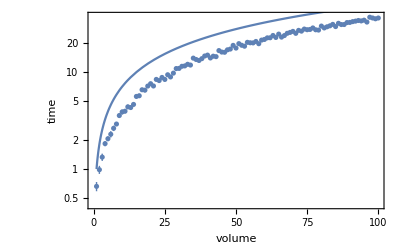

```mathematica
Show[ListLogPlot[majoritysurface2dtimes,Frame->True,FrameLabel->{"volume","time"}],LogPlot[n^0.85,{n,1,100}]] (* line is decent fit to true ising *)
```

```mathematica
majoritysurface3dtimes=Module[{space=30,island=100,dt=100,trials=50,times},Table[
PrintTemporary["Starting island size ",i];
times=Table[RunMajoritySurface[MajorityIslandSurface3D[i,space],dt];fsurfacetime,trials];
{i,Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]},
{i,1,island}]];
```

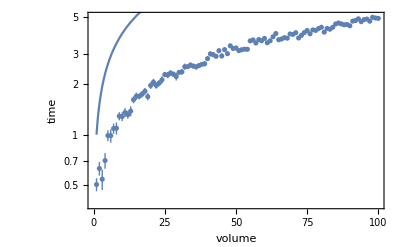

```mathematica
Show[ListLogPlot[majoritysurface3dtimes,Frame->True,FrameLabel->{"volume","time"}],LogPlot[n^0.6,{n,1,100}]] (* line is decent fit to true ising *)
```

We’ve looked at cleaning up islands.  How about search?

```mathematica
isingsurface1dspacetimes=Module[{space=100,dt=100,trials=50,times,start=SessionTime[]},Table[
If[SessionTime[]-start>300,{n,0},
PrintTemporary["Starting random space size ",n];start=SessionTime[];
times=Table[RunIsingSurface[IsingRandomSurface1D[n],dt];fsurfacetime,trials];
{n,Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]}],
{n,1,space}]];
```

```mathematica
majoritysurface1dspacetimes=Module[{space=100,dt=100,trials=50,times,start=SessionTime[]},Table[
If[SessionTime[]-start>300,{n,0},
PrintTemporary["Starting random space size ",n];start=SessionTime[];
times=Table[RunMajoritySurface[MajorityRandomSurface1D[n],dt];fsurfacetime,trials];
{n,Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]}],
{n,1,space}]];
```

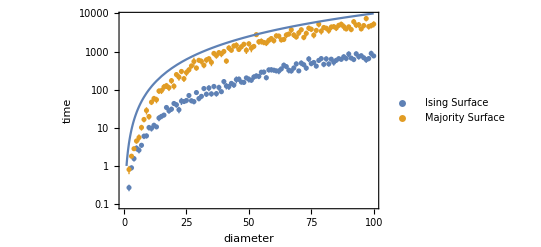

```mathematica
isingsurface1dspacetimes=DeleteCases[isingsurface1dspacetimes,{_,0}];
majoritysurface1dspacetimes=DeleteCases[majoritysurface1dspacetimes,{_,0}];
Show[ListLogPlot[{isingsurface1dspacetimes,majoritysurface1dspacetimes},PlotRange->All,PlotLegends->{"Ising Surface","Majority Surface"},Frame->True,FrameLabel->{"diameter","time"}],LogPlot[r^2,{r,1,100}]]
```

```mathematica
isingsurface2dspacetimes=Module[{space=50,dt=100,trials=50,times,start=SessionTime[]},Table[
If[SessionTime[]-start>300,{n,0},
PrintTemporary["Starting random space size ",n];start=SessionTime[];
times=Table[RunIsingSurface[IsingRandomSurface2D[n],dt];fsurfacetime,trials];
{n,Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]}],
{n,1,space}]];
```

```mathematica
majoritysurface2dspacetimes=Module[{space=50,dt=100,trials=50,times,start=SessionTime[]},Table[
If[SessionTime[]-start>300,{n,0},
PrintTemporary["Starting random space size ",n];start=SessionTime[];
times=Table[RunMajoritySurface[MajorityRandomSurface2D[n],dt];fsurfacetime,trials];
{n,Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]}],
{n,1,space}]];
```

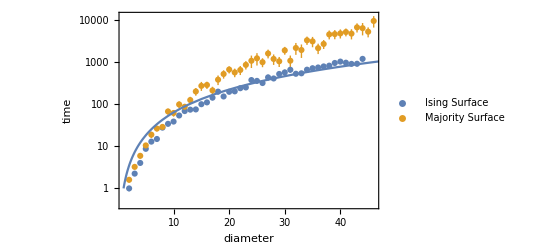

```mathematica
isingsurface2dspacetimes=DeleteCases[isingsurface2dspacetimes,{_,0}];
majoritysurface2dspacetimes=DeleteCases[majoritysurface2dspacetimes,{_,0}];
Show[ListLogPlot[{isingsurface2dspacetimes,majoritysurface2dspacetimes},PlotRange->All,PlotLegends->{"Ising Surface","Majority Surface"},Frame->True,FrameLabel->{"diameter","time"}],LogPlot[r^1.8,{r,1,100}]]
```

```mathematica
isingsurface3dspacetimes=Module[{space=50,dt=100,trials=50,times,start=SessionTime[]},Table[
If[SessionTime[]-start>300,{n,0},
PrintTemporary["Starting random space size ",n];start=SessionTime[];
times=Table[RunIsingSurface[IsingRandomSurface3D[n],dt];fsurfacetime,trials];
{n,Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]}],
{n,1,space}]];
```

```mathematica
majoritysurface3dspacetimes=Module[{space=50,dt=100,trials=50,times,start=SessionTime[]},Table[
If[SessionTime[]-start>300,{n,0},
PrintTemporary["Starting random space size ",n];start=SessionTime[];
times=Table[RunMajoritySurface[MajorityRandomSurface3D[n],dt];fsurfacetime,trials];
{n,Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]}],
{n,1,space}]];
```

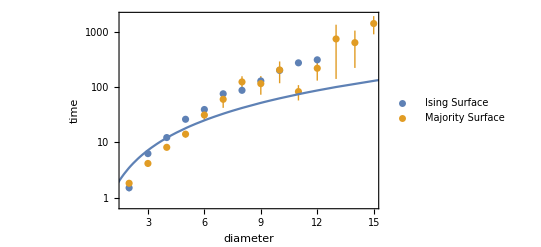

```mathematica
isingsurface3dspacetimes=DeleteCases[isingsurface3dspacetimes,{_,0}];
majoritysurface3dspacetimes=DeleteCases[majoritysurface3dspacetimes,{_,0}];
Show[ListLogPlot[{isingsurface3dspacetimes,majoritysurface3dspacetimes},PlotRange->All,PlotLegends->{"Ising Surface","Majority Surface"},Frame->True,FrameLabel->{"diameter","time"}],LogPlot[r^1.8,{r,1,100}]]
```

Getting trapped in a half-half configuration seems to be a real problem, so it becomes like the unbiased random walk of the 1D case but slower, because it is a surface doing the random walk.

Can a Tabu-like mechanism induce  linear-time waves of change propagating through the system, thus producing a clean sweep that results in consistent coloring?  Yes, but the dynamics are VERY sensitive to the rate constants, with some parameters giving spectacular failures!  In an attempt to avoid such spectacular failures, here we will reset the “slow” rate 0.1 to a value inversely proportional to the diameter of the space.

```mathematica
TabuMajorityCRN={rxn[X+Y,U+U,1],rxn[U+Y,y+y,1],rxn[U+X,x+x,1],rxn[x+Y,x+x,1],rxn[y+X,y+y,1],rxn[x,X,0.1],rxn[y,Y,0.1],rxn[x+y,U+U,1],rxn[x+U,x+x,1],rxn[y+U,y+y,1]};
TabuMajorityRandomSurface1D[n_]:={{Table[RandomChoice[{X,Y}],n]}}
TabuMajorityRandomSurface2D[n_]:={Table[RandomChoice[{X,Y}],n,n]}
TabuMajorityRandomSurface3D[n_]:=Table[RandomChoice[{X,Y}],n,n,n]
TabuMajorityIslandSurface1D[i_,space_]:={{Table[X,space]~Join~Table[Y,i]~Join~Table[X,space]}}
TabuMajorityIslandSurface2D[i_,space_]:={ArrayPad[ArrayReshape[Table[Y,i],{Ceiling[Sqrt[i]],Ceiling[Sqrt[i]]},X],space,X]}
TabuMajorityIslandSurface3D[i_,space_]:=ArrayPad[ArrayReshape[Table[Y,i],{Ceiling[i^(1/3)],Ceiling[i^(1/3)],Ceiling[i^(1/3)]},X],space,X]
TabuMajorityColoring={X->Black,Y->White,U->Red,x->Blue,y->Pink};
```

```mathematica
(* we'll use global variables *)
RunTabuMajoritySurface[surface_,dt_,pause_:0]:=Module[{},
surfaceCRN=TabuMajorityCRN/.{0.1->0.5/(Max@@Dimensions[surface])};
surfacecoloring=TabuMajorityColoring/.If[Length[surface]>1,{Black->Empty},{}];
fsurfaceCRN=PreprocessFasterSurfaceCRN[surfaceCRN,surface];
fsurface=Convert2FasterSpace[surface,fsurfaceCRN];
fsurfacecoloring=Convert2FasterColoring[surfacecoloring,fsurfaceCRN]; 
fsurfacetime=0;haltedq=0;
While[haltedq==0,Pause[pause];{{ddt,eventcount,haltedq},fsurface}=InfoRunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];fsurfacetime+=ddt];
]
```

```mathematica
Dynamic[If[Length[fsurface]==1,
ArrayPlot[First[fsurface],ColorRules->fsurfacecoloring,PlotLabel->fsurfacetime,ImageSize->Large], (* for 1D and 2D *)
ShowSurface3D[fsurface,fsurfacecoloring,PlotLabel->fsurfacetime] (* for 3D *)
]]
```

```mathematica
RunTabuMajoritySurface[TabuMajorityRandomSurface1D[300],1.0,0.1]
```

```mathematica
RunTabuMajoritySurface[TabuMajorityIslandSurface1D[20,300],1.0,0.1]
```

```mathematica
RunTabuMajoritySurface[TabuMajorityRandomSurface2D[100],1.0]
```

```mathematica
RunTabuMajoritySurface[TabuMajorityIslandSurface2D[30,100],1.0]
```

```mathematica
RunTabuMajoritySurface[TabuMajorityRandomSurface3D[20],1.0]
```

```mathematica
RunTabuMajoritySurface[TabuMajorityIslandSurface3D[20,20],1.0]
```

It’s not at all clear that this will be an advantage...

```mathematica
tabumajoritysurface1dspacetimes=Module[{space=100,dt=100,trials=50,times,start=SessionTime[]},Table[
If[SessionTime[]-start>300,{n,0},
PrintTemporary["Starting random space size ",n];start=SessionTime[];
times=Table[RunTabuMajoritySurface[TabuMajorityRandomSurface1D[n],dt];fsurfacetime,trials];
{n,Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]}],
{n,1,space}]];
```

```mathematica
tabumajoritysurface2dspacetimes=Module[{space=100,dt=100,trials=50,times,start=SessionTime[]},Table[
If[SessionTime[]-start>300,{n,0},
PrintTemporary["Starting random space size ",n];start=SessionTime[];
times=Table[RunTabuMajoritySurface[TabuMajorityRandomSurface2D[n],dt];fsurfacetime,trials];
{n,Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]}],
{n,1,space}]];
```

```mathematica
tabumajoritysurface3dspacetimes=Module[{space=100,dt=100,trials=50,times,start=SessionTime[]},Table[
If[SessionTime[]-start>300,{n,0},
PrintTemporary["Starting random space size ",n];start=SessionTime[];
times=Table[RunTabuMajoritySurface[TabuMajorityRandomSurface3D[n],dt];fsurfacetime,trials];
{n,Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]}],
{n,1,space}]];
```

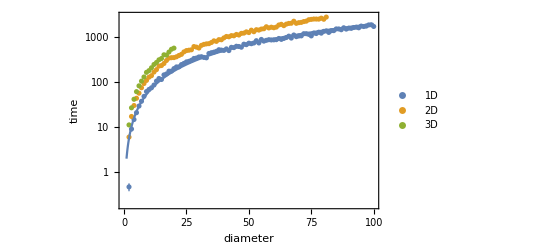

```mathematica
tabumajoritysurface1dspacetimes=DeleteCases[tabumajoritysurface1dspacetimes,{_,0}];
tabumajoritysurface2dspacetimes=DeleteCases[tabumajoritysurface2dspacetimes,{_,0}];
tabumajoritysurface3dspacetimes=DeleteCases[tabumajoritysurface3dspacetimes,{_,0}];
Show[ListLogPlot[{tabumajoritysurface1dspacetimes,tabumajoritysurface2dspacetimes,tabumajoritysurface3dspacetimes},PlotRange->All,PlotLegends->{"1D","2D","3D"},Frame->True,FrameLabel->{"diameter","time"}],LogPlot[2r^1.5,{r,1,100}]]
```

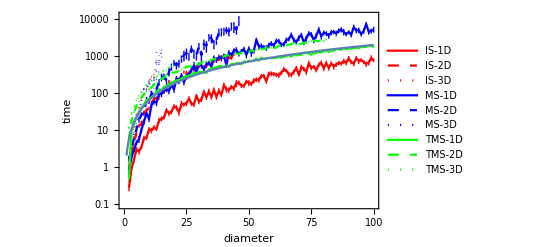

```mathematica
Show[ListLogPlot[{isingsurface1dspacetimes,isingsurface2dspacetimes,isingsurface3dspacetimes,majoritysurface1dspacetimes,majoritysurface2dspacetimes,majoritysurface3dspacetimes,tabumajoritysurface1dspacetimes,tabumajoritysurface2dspacetimes,tabumajoritysurface3dspacetimes},PlotRange->All,Joined->True,PlotStyle->{{Red},{Red,Dashed},{Red,Dotted},{Blue},{Blue,Dashed},{Blue,Dotted},{Green},{Green,Dashed},{Green,Dotted}},PlotLegends->{"IS-1D","IS-2D","IS-3D","MS-1D","MS-2D","MS-3D","TMS-1D","TMS-2D","TMS-3D"},Frame->True,FrameLabel->{"diameter","time"}],LogPlot[2r^1.5,{r,1,100}]]
```

The above illustrate a variety of surface CRN algorithms that, more or less, fail to effectively solve even the simplest and easiest of coloring problems.   Yet they probably reflect the general characteristics of how the currently-envisioned general K-coloring algorithms would deal with these problems.

## Let’s examine a surface CRN version of Pippa’s WalkColoringCRN (aka my “Mild” version)

```mathematica
MildWalkColoringCRN[G_,k_,slow_,fast_]:=Flatten[Join[
Table[rxn[V[v],Try[v,c],1],{v,VertexList[G]},{c,Range[k]}],  (* a vertex without a color will randomly choose a color to try *)
Table[rxn[Try[v,c],V[v,c],slow],{v,VertexList[G]},{c,Range[k]}],  (* if the trial is not quickly rejected, explore it actively *)Table[rxn[V[First[e],c]+V[Last[e],c],V[First[e],c]+V[Last[e]],1],{e,EdgeList[G]},{c,Range[k]}], (* conflicting edges recolor *)
Table[rxn[V[First[e],c]+V[Last[e],c],V[First[e]]+V[Last[e],c],1],{e,EdgeList[G]},{c,Range[k]}], (* conflicting edges recolor *)
Table[rxn[V[First[e],c]+Try[Last[e],c],V[First[e],c]+V[Last[e]],fast],{e,EdgeList[G]},{c,Range[k]}], (* conflicting trials get rejected *)
Table[rxn[Try[First[e],c]+V[Last[e],c],V[First[e]]+V[Last[e],c],fast],{e,EdgeList[G]},{c,Range[k]}], (* conflicting trials get rejected *)
Table[conc[V[v],1],{v,VertexList[G]}] (* each vertex starts uncolored *)
]]
```

```mathematica
SurfaceWalkColoringCRN[k_,slow_,fast_]:=Union[Flatten[{
Table[If[c1=!=c2,
{ 
rxn[v[c1]+v[c2],v[c2]+v[c2],1],(* neighboring v must agree; if not, one randomly chooses to recolor *)
rxn[v[c1]+e[c2],v[c1]+e[c1],1],(* v and neighboring e must agree; if not, one randomly follows the other *)
rxn[v[c1]+e[c2],v[c2]+e[c2],1],
rxn[e[c1]+e[c1],e[c1]+trye[c2],slow/100],    (* adjacent edge sites must be different; if not, one randomly tries to change *)
rxn[v[c1]+trye[c2],tryv[c2]+trye[c2],fast], (* edges initiate trials, which propagate to the region *)
rxn[tryv[c2]+e[c1],tryv[c2]+trye[c2],fast], (* trial colors propagate to other edges *)
rxn[v[c1]+tryv[c2],tryv[c2]+tryv[c2],fast], (* new trial colors propagate throughout the region *)
rxn[tryv[c2],v[c2],slow],(* slowly solidify trials *)
rxn[trye[c2],e[c2],slow],(* slowly solidify trials *)
rxn[v[c2]+tryv[c2],v[c2]+v[c2],fast], (* if a trial color solidifies anywhere, the solidification propagates *)
rxn[v[c2]+trye[c2],v[c2]+e[c2],fast], (* solidification propagates to edges *)
rxn[e[c2]+trye[c2],e[c2]+trye[c1],1] (* how does a trial color change get rejected? choose something else to try *)
},{}],
{c1,1,k},{c2,1,k}]
}]]
WalkColoringRules[k_]:=With[{colors={Red,Green,Lighter[Blue],Black},trycolors={LightPink,LightGreen,LightMagenta,LightBrown}},
Flatten[Join[
{w->White},
Table[{v[i]->Darker[colors[[i]]],e[i]->Lighter[colors[[i]]]},{i,1,k}],
Table[{tryv[i]->Darker[trycolors[[i]]],trye[i]->Lighter[trycolors[[i]]]},{i,1,k}]
]]]
```

```mathematica
PrepareWalkColoringLayout[option_]:=Module[{map,graph,k},
Switch[option,
0,{map,graph}=RandomSquareColoringMap[20,40,0,1];k=2,
1,{map,graph}=RandomSquareColoringMap[20,40,0.1,.7];k=4,
2,{map,graph}=RandomSquareColoringMap[20,40,0.2,.5];k=3,
3,{map,graph}=RandomSquareColoringMap[20,20,0.35,.25];k=3,
4,{map,graph}=RandomSquareColoringMap[10,10,0.5,0.5];k=3
];
Print[If[SatisfiableQ[ColoringSAT[graph,k]],"Colorable!","Not colorable!"]];
fsurfaceCRNorig=SurfaceWalkColoringCRN[k,.1,10];
fsurfaceorig=map;
fsurfacecoloringorig=WalkColoringRules[k];
fsurfaceCRN=PreprocessFasterSurfaceCRN[fsurfaceCRNorig,{fsurfaceorig}];
fsurface=Convert2FasterSpace[{fsurfaceorig},fsurfaceCRN];
fsurfacecoloring=Convert2FasterColoring[ fsurfacecoloringorig,fsurfaceCRN];
fsurfacetime=0;
]
```

```mathematica
PrepareWalkColoringLayout[2]
```

Colorable!

```mathematica
Dynamic[ArrayPlot[First[fsurface],ColorRules->fsurfacecoloring,PlotLabel->{fsurfacetime,fevents},ImageSize->800]]
```

```mathematica
haltedq=0;fevents=0;
With[{dt=10},While[haltedq==0,{{ddt,eventcount,haltedq},fsurface}=InfoRunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];fsurfacetime+=ddt;fevents+=eventcount]]
```

This very much does not work well!   It just gets stuck going back and forth...  until I change the edge-conflict-detection reaction from rate 1 to rate slow/100.

But the number of events is still about 10^6 for layout 2  -- about the same as the original, or rather 2x worse.

## Let’s try a surface CRN version of some kind of Tabu Search.

I am reminded of “SPIRAL WAVE STRUCTURE IN PRE-BIOTIC EVOLUTION: HYPERCYCLES STABLE AGAINST PARASITES” M.C. BOERLIJST and P. HOGEWEG (1991), combined with Chris Thachuk’s comments about 2-SAT and the value of linear propagation of inference.  Could spiral dynamics be good for spatial SAT-solvers, map-coloring, and other constraint satisfaction problems?  Would a TabuCol-like dynamics give rise to spirals here? 

The TabuMajorityCRN, above, works only for the fully-connected square lattice, which is 2-colorable.  Here we’ll adapt to the arbitrary graph layout framework.  As keeping a full tabu list in a single site requires many more states, we won’t explore that possibility yet.  Instead of color-specific tabu, we’ll just freeze a node from changing for a while.

```mathematica
SurfaceFreezeColoringCRN[k_,slow_]:=Union[Flatten[{
Table[If[c1=!=c2,
{ 
rxn[v[c1]+v[c2],V[c2]+v[c2],1],(* neighboring v must agree; if not, one randomly chooses to recolor and freezes *)
rxn[v[c1]+V[c2],V[c2]+V[c2],1],(* frozen nodes are fully impactful on their neighbors *)
rxn[v[c1]+e[c2],v[c1]+e[c1],1],(* v and neighboring e must agree; if not, one randomly follows the other *)
rxn[v[c1]+e[c2],V[c2]+e[c2],1],(* e edges won't bother to freeze, but if a v recolors, it freezes *)
rxn[V[c1]+e[c2],V[c1]+e[c1],1],
rxn[e[c1]+e[c1],e[c1]+e[c2],slow/100],    (* adjacent edge sites must be different; if not, one randomly changes *)
rxn[V[c2],v[c2],slow] (* slowly melt frozen nodes, allowing them to change again  *)
},{}],
{c1,1,k},{c2,1,k}]
}]]
FreezeColoringRules[k_]:=With[{colors={Red,Green,Lighter[Blue],Black},freezecolors={LightPink,LightGreen,LightMagenta,LightBrown}},
Flatten[Join[
{w->White},
Table[{v[i]->Lighter[colors[[i]]],e[i]->Darker[colors[[i]]]},{i,1,k}],
Table[{V[i]->freezecolors[[i]]},{i,1,k}]
]]]
```

```mathematica
PrepareFreezeColoringLayout[option_,slow_]:=Module[{map,graph,k},
Switch[option,
0,{map,graph}=RandomSquareColoringMap[20,40,0,1];k=2,
1,{map,graph}=RandomSquareColoringMap[20,40,0.1,.7];k=4,
2,{map,graph}=RandomSquareColoringMap[20,40,0.2,.5];k=3,
3,{map,graph}=RandomSquareColoringMap[20,20,0.35,.25];k=3,
4,{map,graph}=RandomSquareColoringMap[10,10,0.5,0.5];k=3
];
Print[If[SatisfiableQ[ColoringSAT[graph,k]],"Colorable!","Not colorable!"]];
fsurfaceCRNorig=SurfaceFreezeColoringCRN[k,slow];
fsurfaceorig=map;
fsurfacecoloringorig=FreezeColoringRules[k];
fsurfaceCRN=PreprocessFasterSurfaceCRN[fsurfaceCRNorig,{fsurfaceorig}];
fsurface=Convert2FasterSpace[{fsurfaceorig},fsurfaceCRN];
fsurfacecoloring=Convert2FasterColoring[ fsurfacecoloringorig,fsurfaceCRN];
fsurfacetime=0;
]
```

```mathematica
PrepareFreezeColoringLayout[2,10]   (* slow = 0.1 doesn't work; slow = 10 works no better than original, maybe 5x worse *)
```

Colorable!

```mathematica
Dynamic[ArrayPlot[First[fsurface],ColorRules->fsurfacecoloring,PlotLabel->{fsurfacetime,fevents},ImageSize->800]]
```

```mathematica
haltedq=0;fevents=0;
With[{dt=10},While[haltedq==0,{{ddt,eventcount,haltedq},fsurface}=InfoRunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];fsurfacetime+=ddt;fevents+=eventcount]]
```

```mathematica
(RevertFaster2Space[First[#],fsurfaceCRN]->Last[#])& /@fsurfacecoloring
```

{w→GrayLevel[1],v[1]→RGBColor[1, Rational[1, 3], Rational[1, 3]],e[1]→RGBColor[Rational[2, 3], 0, 0],v[2]→RGBColor[Rational[1, 3], 1, Rational[1, 3]],e[2]→RGBColor[0, Rational[2, 3], 0],v[3]→RGBColor[Rational[5, 9], Rational[5, 9], 1],e[3]→RGBColor[Rational[2, 9], Rational[2, 9], Rational[2, 3]],V[1]→RGBColor[1, 0.925, 0.925],V[2]→RGBColor[0.88, 1, 0.88],V[3]→RGBColor[1, 0.9, 1]}

## Let’s try a surface CRN version of a propagating wave.

Disagreements will be detected rarely  at edge pairs; the random recoloring will propagate through the region; etc.
E is E\[ Null ]

```mathematica
SurfaceWaveColoringCRN[k_,slow_]:=Union[Flatten[{
Table[If[c1=!=c2,
{ 
rxn[v[c1]+v[c2],v[c2]+v[c2],slow],(* neighboring v must agree; if not, one randomly chooses to recolor but doesn't freeze *)
rxn[v[c1]+e[c2],v[c1]+e[c1],slow],(* v and neighboring e must agree; if not, one randomly follows the other *)
rxn[v[c1]+e[c2],v[c2]+e[c2],slow],(* v and neighboring e must agree; if not, one randomly follows the other *)
rxn[v[c1]+V[c2],V[c2]+V[c2],1],(* recolored/frozen nodes pass their new color to their neighbors, and freeze them *)
rxn[v[c1]+E[c2],V[c2]+E[c2],1],(* recolored edges propagate their change and freeze vertex sites *)
rxn[V[c1]+e[c2],V[c1]+e[c1],1], (* recolored vertex sites pass their color to outgoing edges *)
rxn[e[c1]+e[c1],e[c1]+E[c2],slow/100],    (* adjacent edge sites must be different; if not, one randomly changes & freezes *)
rxn[V[c2],v[c2],slow], (* slowly melt frozen nodes, allowing them to change again  *)
rxn[E[c2],e[c2],slow] (* slowly melt frozen nodes, allowing them to change again  *)
},{}],
{c1,1,k},{c2,1,k}]
}]]
WaveColoringRules[k_]:=With[{colors={Red,Green,Lighter[Blue],Black},freezecolors={LightPink,LightGreen,LightMagenta,LightBrown}},
Flatten[Join[
{w->White},
Table[{v[i]->Lighter[colors[[i]]],e[i]->Darker[colors[[i]]]},{i,1,k}],
Table[{V[i]->freezecolors[[i]],E[i]->Darker[freezecolors[[i]]]},{i,1,k}]
]]]
```

```mathematica
PrepareWaveColoringLayout[option_,slow_]:=Module[{map,graph,k},
Switch[option,
0,{map,graph}=RandomSquareColoringMap[20,40,0,1];k=2,
1,{map,graph}=RandomSquareColoringMap[20,40,0.1,.7];k=4,
2,{map,graph}=RandomSquareColoringMap[20,40,0.2,.5];k=3,
3,{map,graph}=RandomSquareColoringMap[20,20,0.35,.25];k=3,
4,{map,graph}=RandomSquareColoringMap[10,10,0.5,0.5];k=3
];
Print[If[SatisfiableQ[ColoringSAT[graph,k]],"Colorable!","Not colorable!"]];
fsurfaceCRNorig=SurfaceWaveColoringCRN[k,slow];
fsurfaceorig=map;
fsurfacecoloringorig=WaveColoringRules[k];
fsurfaceCRN=PreprocessFasterSurfaceCRN[fsurfaceCRNorig,{fsurfaceorig}];
fsurface=Convert2FasterSpace[{fsurfaceorig},fsurfaceCRN];
fsurfacecoloring=Convert2FasterColoring[ fsurfacecoloringorig,fsurfaceCRN];
fsurfacetime=0;
]
```

```mathematica
PrepareWaveColoringLayout[2,0.5]  (* mysteriously, optimal performance comes from slow between 0.5 and 1 *)
```

Colorable!

```mathematica
Dynamic[ArrayPlot[First[fsurface],ColorRules->fsurfacecoloring,PlotLabel->{fsurfacetime,fevents},ImageSize->800]]
```

```mathematica
haltedq=0;fevents=0;
With[{dt=10},While[haltedq==0,{{ddt,eventcount,haltedq},fsurface}=InfoRunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];fsurfacetime+=ddt;fevents+=eventcount]]
```

```mathematica
(RevertFaster2Space[First[#],fsurfaceCRN]->Last[#])& /@fsurfacecoloring
```

{w→GrayLevel[1],v[1]→RGBColor[1, Rational[1, 3], Rational[1, 3]],e[1]→RGBColor[Rational[2, 3], 0, 0],v[2]→RGBColor[Rational[1, 3], 1, Rational[1, 3]],e[2]→RGBColor[0, Rational[2, 3], 0],v[3]→RGBColor[Rational[5, 9], Rational[5, 9], 1],e[3]→RGBColor[Rational[2, 9], Rational[2, 9], Rational[2, 3]],V[1]→RGBColor[1, 0.925, 0.925],E[1]→RGBColor[Rational[2, 3], 0.6166666666666667, 0.6166666666666667],V[2]→RGBColor[0.88, 1, 0.88],E[2]→RGBColor[0.5866666666666667, Rational[2, 3], 0.5866666666666667],V[3]→RGBColor[1, 0.9, 1],E[3]→RGBColor[Rational[2, 3], 0.6000000000000001, Rational[2, 3]]}

Inexplicably works pretty well -- maybe the best CRN yet... though by 2x at most.  But why?

## Let’s try a surface CRN version of a propagating wave with rejection.

Disagreements will be detected rarely  at edge pairs; the random recoloring will propagate through the region; etc.
E is E\[ Null ]

```mathematica
SurfaceRejectWaveColoringCRN[k_,slow_,fast_]:=Union[Flatten[{
Table[If[c1=!=c2,
{ 
rxn[v[c1]+v[c2],v[c2]+v[c2],slow],(* neighboring v must agree; if not, one randomly chooses to recolor but doesn't freeze *)
rxn[v[c1]+e[c2],v[c1]+e[c1],slow],(* v and neighboring e must agree; if not, one randomly follows the other *)
rxn[v[c1]+e[c2],v[c2]+e[c2],slow],(* v and neighboring e must agree; if not, one randomly follows the other *)

rxn[e[c1]+e[c1],e[c1]+E[c2],slow/100],    (* adjacent edge sites must be different; if not, one randomly changes & freezes *)
rxn[v[c1]+V[c2],V[c2]+V[c2],1],(* recolored/frozen nodes pass their new color to their neighbors, and freeze them *)
rxn[v[c1]+E[c2],V[c2]+E[c2],1],(* recolored edges propagate their change and freeze vertex sites *)
rxn[V[c1]+e[c2],V[c1]+E[c1],1], (* recolored vertex sites pass their color to outgoing edges, which will initially be frozen *)

rxn[e[c1]+E[c1],e[c1]+E,fast],(* if a recoloring clashes with a neighbor, initiate a fast reversion to restore the original colors *)
rxn[E+V[c1],E+V,fast], (* a rejected edge propagates rejeection to neighboring vertex sites *)
rxn[V+V[c1],V+V,fast], (* a rejected vertex site propagates rejection to neighboring vertex sites *)
rxn[V+E[c1],V+E,fast], (* a rejected vertex site propagates rejection to neighboring edge *)
rxn[v[c1]+V,v[c1]+v[c1],fast],(* a rejected vertex site adopts color of any remaining unchanged site or restored site *)
rxn[v[c1]+E,v[c1]+e[c1],fast],(* a rejected edge adopts color of any remaining unchanged site or restored site *)
rxn[E,e[c1],slow], (* if things got stuck, color somehow *)
rxn[V,v[c1],slow], (* if things got stuck, color somehow *)

rxn[V[c2],v[c2],slow], (* slowly melt frozen nodes, allowing them to change again  *)
rxn[E[c2],e[c2],slow] (* slowly melt frozen nodes, allowing them to change again  *)
},{}],
{c1,1,k},{c2,1,k}]
}]]
RejectWaveColoringRules[k_]:=With[{colors={Red,Green,Lighter[Blue],Black},freezecolors={LightPink,LightGreen,LightMagenta,LightBrown}},
Flatten[Join[
{w->White,E->Yellow,V->Yellow},
Table[{v[i]->Lighter[colors[[i]]],e[i]->Darker[colors[[i]]]},{i,1,k}],
Table[{V[i]->freezecolors[[i]],E[i]->Darker[freezecolors[[i]]]},{i,1,k}]
]]]
```

```mathematica
PrepareRejectWaveColoringLayout[option_,slow_,fast_]:=Module[{map,graph,k},
Switch[option,
0,{map,graph}=RandomSquareColoringMap[20,40,0,1];k=2,
1,{map,graph}=RandomSquareColoringMap[20,40,0.1,.7];k=4,
2,{map,graph}=RandomSquareColoringMap[20,40,0.2,.5];k=3,
3,{map,graph}=RandomSquareColoringMap[20,20,0.35,.25];k=3,
4,{map,graph}=RandomSquareColoringMap[10,10,0.5,0.5];k=3
];
Print[If[SatisfiableQ[ColoringSAT[graph,k]],"Colorable!","Not colorable!"]];
fsurfaceCRNorig=SurfaceRejectWaveColoringCRN[k,slow,fast];
fsurfaceorig=map;
fsurfacecoloringorig=RejectWaveColoringRules[k];
fsurfaceCRN=PreprocessFasterSurfaceCRN[fsurfaceCRNorig,{fsurfaceorig}];
fsurface=Convert2FasterSpace[{fsurfaceorig},fsurfaceCRN];
fsurfacecoloring=Convert2FasterColoring[ fsurfacecoloringorig,fsurfaceCRN];
fsurfacetime=0;
]
```

```mathematica
PrepareRejectWaveColoringLayout[2,10,0.1] (* making slow fast and fast slow seems to work best, again, but why? *)
```

Colorable!

```mathematica
PrepareRejectWaveColoringLayout[2,0.1,10] (* slow being slow and fast being fast seems to go nowhere (except when lucky) *)
```

Colorable!

```mathematica
PrepareRejectWaveColoringLayout[2,0.01,10] (* LATER: as suggested by the PetfordWelsh analysis below, slow being even slower makes this the best CRN! *)
```

Colorable!

```mathematica
Dynamic[ArrayPlot[First[fsurface],ColorRules->fsurfacecoloring,PlotLabel->{fsurfacetime,fevents},ImageSize->800]]
```

```mathematica
haltedq=0;fevents=0;
With[{dt=1/Min[Last/@fsurfaceCRNorig]},While[haltedq==0,{{ddt,eventcount,haltedq},fsurface}=InfoRunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];fsurfacetime+=ddt;fevents+=eventcount]]
```

```mathematica
(RevertFaster2Space[First[#],fsurfaceCRN]->Last[#])& /@fsurfacecoloring
```

{w→GrayLevel[1],E→RGBColor[1, 1, 0],V→RGBColor[1, 1, 0],v[1]→RGBColor[1, Rational[1, 3], Rational[1, 3]],e[1]→RGBColor[Rational[2, 3], 0, 0],v[2]→RGBColor[Rational[1, 3], 1, Rational[1, 3]],e[2]→RGBColor[0, Rational[2, 3], 0],v[3]→RGBColor[Rational[5, 9], Rational[5, 9], 1],e[3]→RGBColor[Rational[2, 9], Rational[2, 9], Rational[2, 3]],V[1]→RGBColor[1, 0.925, 0.925],E[1]→RGBColor[Rational[2, 3], 0.6166666666666667, 0.6166666666666667],V[2]→RGBColor[0.88, 1, 0.88],E[2]→RGBColor[0.5866666666666667, Rational[2, 3], 0.5866666666666667],V[3]→RGBColor[1, 0.9, 1],E[3]→RGBColor[Rational[2, 3], 0.6000000000000001, Rational[2, 3]]}

Beyond the mystery of rate constants, this seems not particularly better than the original (although the original is a simpler CRN).  Worth understanding why... start by optimizing rate constants?
[[See below: making “slow” super-slow squeezes much better performance out of this CRN!]]

A scan of 10x10 maps showed that SurfaceMapColoringCRN had the most trouble around p=0.3, q=0.9.

```mathematica
FindColorableMap[n_,m_,p_,q_,k_]:=Module[{map,graph,SATtime,sat,colorable=False,attempts=0},
While[!colorable,
{map,graph}=RandomSquareColoringMap[n,m,p,q];attempts++;
sat=ColoringSAT[graph,k];{SATtime,colorable}=AbsoluteTiming[SatisfiableQ[sat]]
];
If[attempts>10,Print["It took ",attempts," attempts to find a colorable graph!"]];
{attempts,map,VertexCount[graph],EdgeCount[graph],SATtime}]
```

```mathematica
SurfaceMapColoringTimes[map_,k_]:=Module[{CRNtime,dt=1000},
fsurfaceCRNorig=SurfaceMapColoringCRN[k];
fsurfaceorig=map;
fsurfacecoloringorig=MapColoringRules[k];
fsurfaceCRN=PreprocessFasterSurfaceCRN[fsurfaceCRNorig,{fsurfaceorig}];
fsurface=Convert2FasterSpace[{fsurfaceorig},fsurfaceCRN];
fsurfacecoloring=Convert2FasterColoring[ fsurfacecoloringorig,fsurfaceCRN];
fsurfacetime=0;haltedq=0;
{CRNtime,fsurface}=AbsoluteTiming[
While[haltedq==0,{{ddt,eventcount,haltedq},fsurface}=InfoRunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];fsurfacetime+=ddt];
fsurface
];
CRNtime]
```

```mathematica
MapColoringStats[map_,k_,trials_]:=Module[{data},
data=Table[SurfaceMapColoringTimes[map,k],trials];
Around[Mean[data],StandardDeviation[data]]
]
```

```mathematica
RejectWaveColoringTimes[map_,k_,slow_:1,fast_:1]:=Module[{CRNtime,dt=1000},
fsurfaceCRNorig=SurfaceRejectWaveColoringCRN[k,slow,fast];
fsurfaceorig=map;
fsurfacecoloringorig=RejectWaveColoringRules[k];
fsurfaceCRN=PreprocessFasterSurfaceCRN[fsurfaceCRNorig,{fsurfaceorig}];
fsurface=Convert2FasterSpace[{fsurfaceorig},fsurfaceCRN];
fsurfacecoloring=Convert2FasterColoring[ fsurfacecoloringorig,fsurfaceCRN];
fsurfacetime=0;haltedq=0;
{CRNtime,fsurface}=AbsoluteTiming[
While[haltedq==0,{{ddt,eventcount,haltedq},fsurface}=InfoRunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];fsurfacetime+=ddt];
fsurface
];
CRNtime]
```

```mathematica
RejectWaveColoringStats[map_,k_,slow_,fast_,trials_]:=Module[{data},
data=Table[RejectWaveColoringTimes[map,k,slow,fast],trials];
Around[Mean[data],StandardDeviation[data]]
]
```

```mathematica
referencemap=FindColorableMap[10,10,0.3,0.9,3][[2]];
```

```mathematica
MapColoringStats[referencemap,3,10]
```

6.5.

```mathematica
RejectWaveColoringStats[referencemap,3,10,.1,10]
```

8.9.

```mathematica
RejectWaveColoringStats[referencemap,3,5,.1,10]
```

5.4.

```mathematica
RejectWaveColoringStats[referencemap,3,10,.2,10]
```

6.5.

```mathematica
RejectWaveColoringStats[referencemap,3,2,.1,10]
```

7.8.

```mathematica
RejectWaveColoringStats[referencemap,3,10,.5,10]
```

6.7.

```mathematica
RejectWaveColoringStats[referencemap,3,5,.2,10]
```

6.6.

Well, this isn’t super-hopeful.    The original surface CRN remains the best.   Unless there are some unexpected parameter settings out there.  Actually, SurfaceWaveColoringCRN is better than the original.  Hmmm.

```mathematica
(* now with super-slow slowness as suggested by Petford-Welsh analysis below... best yet *)
RejectWaveColoringStats[referencemap,3,0.01,10,100]
```

2.01.9

Still, it seems to me that the probabilistic logic of Petford-Welsh ought to be feasible to implement by assessing the probability of recoloring a region based on the number of changes of rejecting the recoloring.

What we want to ask is, given the initial detection of a coloring conflict, conditioned on neighboring regions not recoloring for outside reasons, what is the probability that the central region will choose a new color as a function of the neighboring colors.  We can answer that by simulating a central region with a few unconnected neighbors.  More specifically, given N,E,S,W neighbor colors {c1,c2,c3,c4} and the central region being color c0, after a (mocked-up) reaction that triggers one edge to detect a problem and initiate a change in the central region, what is the final stable configuration {c1’,c2’,c3’,c4’}+{c0’}, and how long did it take to get there?   The time matters because we want to know whether it’s reasonable to assume that a given region recolors to completion before a neighboring region recolors from other causes.  Without loss of generality, we choose c0=1 and c1=1 so that there is definitely a clash on that edge... and perhaps others as well.

Let #1, #2, ... #k be the number of neighbors with the given color.  If #1>1 then there is another edge simultaneously in conflict; but if we change the central color, those edges will also be fixed.  It would be convenient if edge conflict detection is rare relative to changes within a node, in which case the result of stabilizing a color change will not depend on whether there are other initial conflict, and will just depend on potential new conflicts.  This would allow us to justify coarse-graining the dynamics into individual region-recoloring events, separated by edge-conflict detection reactions.  That is, after each edge-conflict detection reaction, we allow and follow all other reaction types until no more non-edge-conflict reactions are possible -- resulting in a valid state inside the region.

In short, we use simulation to estimate the probability Prob( c0’ = c |  {c1,c2,c3,c4}+{c0} ), where all e[i]+e[i] reactions have been turned off, and the initial state includes the effect of one of them.

```mathematica
AssessPetfordWelsh[crn_,newedge_,{c1_,c2_,c3_,c4_},c0_,trials_:1000]:=Module[{template,map,data,dt=If[trials==-1,0.1,100]},
(* trials == -1 means to ddo one trial, very slowly, so it can be watched with a dynamic printout *)
template={
{w,w,w,w,w,v,w,w,w,w,w},
{w,w,w,w,w,e,w,w,w,w,w},
{w,w,w,w,w,e,w,w,w,w,w},
{w,w,w,v,v,v,v,v,w,w,w},
{w,w,w,v,v,v,v,v,w,w,w},
{v,e,e,v,v,v,v,v,e,e,v},
{w,w,w,v,v,v,v,v,w,w,w},
{w,w,w,v,v,v,v,v,w,w,w},
{w,w,w,w,w,e,w,w,w,w,w},
{w,w,w,w,w,e,w,w,w,w,w},
{w,w,w,w,w,v,w,w,w,w,w}
};
map=template/.{v->v[c0],e->e[c0]};
map[[1,6]]=v[c1];map[[2,6]]=e[c1];
map[[6,11]]=v[c2];map[[6,10]]=e[c2];
map[[11,6]]=v[c3];map[[10,6]]=e[c3];
map[[6,1]]=v[c4];map[[6,2]]=e[c4];
map[[3,6]]=newedge;
data=Table[
fsurfaceCRNorig=Cases[crn,Except[rxn[e[_]+e[_],_,_]]];
fsurfaceorig=map;
fsurfaceCRN=PreprocessFasterSurfaceCRN[fsurfaceCRNorig,{fsurfaceorig}];
fsurface=Convert2FasterSpace[{fsurfaceorig},fsurfaceCRN];
fsurfacetime=0;haltedq=0;
While[haltedq==0,
{{ddt,eventcount,haltedq},fsurface}=InfoRunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];
If[trials==-1,Pause[0.1]];];
RevertFaster2Space[fsurface,fsurfaceCRN][[1,6,6]],
{i,Abs[trials]}];
KeySort[Counts[data]]
]
```

```mathematica
SurfaceMapColoringCRN[3]
```

{2 e[1] →^0.01 e[1]+e[2] ,2 e[1] →^0.01 e[1]+e[3] ,v[2]+e[1] →^1 v[1]+e[1] ,v[2]+e[1] →^1 v[2]+e[2] ,v[3]+e[1] →^1 v[1]+e[1] ,v[3]+e[1] →^1 v[3]+e[3] ,2 e[2] →^0.01 e[2]+e[1] ,2 e[2] →^0.01 e[2]+e[3] ,v[1]+e[2] →^1 v[1]+e[1] ,v[1]+e[2] →^1 v[2]+e[2] ,v[3]+e[2] →^1 v[2]+e[2] ,v[3]+e[2] →^1 v[3]+e[3] ,2 e[3] →^0.01 e[3]+e[1] ,2 e[3] →^0.01 e[3]+e[2] ,v[1]+e[3] →^1 v[1]+e[1] ,v[1]+e[3] →^1 v[3]+e[3] ,v[2]+e[3] →^1 v[2]+e[2] ,v[2]+e[3] →^1 v[3]+e[3] ,v[2]+v[1] →^1 2 v[1] ,v[3]+v[1] →^1 2 v[1] ,v[1]+v[2] →^1 2 v[2] ,v[3]+v[2] →^1 2 v[2] ,v[1]+v[3] →^1 2 v[3] ,v[2]+v[3] →^1 2 v[3] }

```mathematica
AssessPetfordWelsh[SurfaceMapColoringCRN[3],e[2],{1,1,1,1},1,10000]
```

<|v[1]→9634,v[2]→366|>

```mathematica
AssessPetfordWelsh[SurfaceMapColoringCRN[3],e[2],{1,2,2,2},1,10000]
```

<|v[1]→9648,v[2]→352|>

```mathematica
AssessPetfordWelsh[SurfaceMapColoringCRN[3],e[2],{1,3,3,3},1,10000]
```

<|v[1]→9693,v[2]→307|>

We don’t expect any dependence on the neighbor colors for the above CRN.  So let’s try one where we do expect a dependence.

```mathematica
SurfaceRejectWaveColoringCRN[3,5,.1]
```

{E →^5 e[1] ,E →^5 e[2] ,E →^5 e[3] ,v[1]+E →^0.1 v[1]+e[1] ,v[2]+E →^0.1 v[2]+e[2] ,v[3]+E →^0.1 v[3]+e[3] ,V →^5 v[1] ,V →^5 v[2] ,V →^5 v[3] ,v[1]+V →^0.1 2 v[1] ,v[2]+V →^0.1 2 v[2] ,v[3]+V →^0.1 2 v[3] ,2 e[1] →^(1/20) e[1]+E[2] ,2 e[1] →^(1/20) e[1]+E[3] ,v[2]+e[1] →^5 v[1]+e[1] ,v[2]+e[1] →^5 v[2]+e[2] ,v[3]+e[1] →^5 v[1]+e[1] ,v[3]+e[1] →^5 v[3]+e[3] ,V[2]+e[1] →^1 V[2]+E[2] ,V[3]+e[1] →^1 V[3]+E[3] ,2 e[2] →^(1/20) e[2]+E[1] ,2 e[2] →^(1/20) e[2]+E[3] ,v[1]+e[2] →^5 v[1]+e[1] ,v[1]+e[2] →^5 v[2]+e[2] ,v[3]+e[2] →^5 v[2]+e[2] ,v[3]+e[2] →^5 v[3]+e[3] ,V[1]+e[2] →^1 V[1]+E[1] ,V[3]+e[2] →^1 V[3]+E[3] ,2 e[3] →^(1/20) e[3]+E[1] ,2 e[3] →^(1/20) e[3]+E[2] ,v[1]+e[3] →^5 v[1]+e[1] ,v[1]+e[3] →^5 v[3]+e[3] ,v[2]+e[3] →^5 v[2]+e[2] ,v[2]+e[3] →^5 v[3]+e[3] ,V[1]+e[3] →^1 V[1]+E[1] ,V[2]+e[3] →^1 V[2]+E[2] ,E[1] →^5 e[1] ,V+E[1] →^0.1 V+E ,e[1]+E[1] →^0.1 e[1]+E ,v[2]+E[1] →^1 V[1]+E[1] ,v[3]+E[1] →^1 V[1]+E[1] ,E[2] →^5 e[2] ,V+E[2] →^0.1 V+E ,e[2]+E[2] →^0.1 e[2]+E ,v[1]+E[2] →^1 V[2]+E[2] ,v[3]+E[2] →^1 V[2]+E[2] ,E[3] →^5 e[3] ,V+E[3] →^0.1 V+E ,e[3]+E[3] →^0.1 e[3]+E ,v[1]+E[3] →^1 V[3]+E[3] ,v[2]+E[3] →^1 V[3]+E[3] ,v[2]+v[1] →^5 2 v[1] ,v[3]+v[1] →^5 2 v[1] ,v[1]+v[2] →^5 2 v[2] ,v[3]+v[2] →^5 2 v[2] ,v[1]+v[3] →^5 2 v[3] ,v[2]+v[3] →^5 2 v[3] ,V[1] →^5 v[1] ,E+V[1] →^0.1 E+V ,V+V[1] →^0.1 2 V ,v[2]+V[1] →^1 2 V[1] ,v[3]+V[1] →^1 2 V[1] ,V[2] →^5 v[2] ,E+V[2] →^0.1 E+V ,V+V[2] →^0.1 2 V ,v[1]+V[2] →^1 2 V[2] ,v[3]+V[2] →^1 2 V[2] ,V[3] →^5 v[3] ,E+V[3] →^0.1 E+V ,V+V[3] →^0.1 2 V ,v[1]+V[3] →^1 2 V[3] ,v[2]+V[3] →^1 2 V[3] }

```mathematica
AssessPetfordWelsh[SurfaceRejectWaveColoringCRN[3,5,.1],E[2],{1,1,1,1},1,10000] (* that's E \[ Null ] to you! *)
```

<|v[1]→9525,v[2]→475|>

```mathematica
AssessPetfordWelsh[SurfaceRejectWaveColoringCRN[3,5,.1],E[2],{1,2,2,2},1,10000]
```

<|v[1]→9535,v[2]→465|>

```mathematica
AssessPetfordWelsh[SurfaceRejectWaveColoringCRN[3,5,.1],E[2],{1,2,2,3},1,10000]
```

<|v[1]→9555,v[2]→445|>

```mathematica
AssessPetfordWelsh[SurfaceRejectWaveColoringCRN[3,5,.1],E[2],{1,2,3,3},1,10000]
```

<|v[1]→9558,v[2]→442|>

```mathematica
AssessPetfordWelsh[SurfaceRejectWaveColoringCRN[3,5,.1],E[2],{1,3,3,3},1,10000]
```

<|v[1]→9553,v[2]→447|>

It is surprising that so many revert back to 1, and that there is no dependence on the number of 2 neighbors that ought to reject the attempt.

But it shouldn’t be surprising!  With slow=5, the E and V species quickly revert back to e and v, allowing random competition prior to any rejection stage being involved.

```mathematica
Dynamic[First[RevertFaster2Space[fsurface,fsurfaceCRN]]//MatrixForm]
```

```mathematica
AssessPetfordWelsh[SurfaceRejectWaveColoringCRN[3,5,.1],E[2],{1,2,2,3},1,-1]
```

<|v[1]→1|>

```mathematica
AssessPetfordWelsh[SurfaceRejectWaveColoringCRN[3,.1,5],E[2],{1,2,2,3},1,-1]
```

<|v[2]→1|>

Make “slow” actually slow, and it behaves more like we intended... especially if we make “slow” really slow.   More 2 neighbors results in few of the attempts to recolor as 2 actually being successful.  (Most fail by reverting back to 1, but this CRN allows jammed configurations to randomly recolor, so we also get a few 3s.)   The results are disappointing, because we wanted (as per Petford-Welsh) the probability of success of an attempt to recolor as 2 to decrease as α^-#2 for e.g. α=4, but instead it just decreases a little bit -- about a factor of 2 total.

```mathematica
Table[{"#2s = "<>ToString[3-r]<>":   ",
AssessPetfordWelsh[SurfaceRejectWaveColoringCRN[3,.1,10],E[2],{1,2+Boole[r>0],2+Boole[r>1],2+Boole[r>2]},1,10000]},
{r,0,3}]//MatrixForm
```

(#2s = 3:    | <|v[1]→1677,v[2]→8260,v[3]→63|>
#2s = 2:    | <|v[1]→1316,v[2]→8632,v[3]→52|>
#2s = 1:    | <|v[1]→1134,v[2]→8839,v[3]→27|>
#2s = 0:    | <|v[1]→914,v[2]→9086|>)

```mathematica
Table[{"#2s = "<>ToString[3-r]<>":   ",
AssessPetfordWelsh[SurfaceRejectWaveColoringCRN[3,.01,10],E[2],{1,2+Boole[r>0],2+Boole[r>1],2+Boole[r>2]},1,10000]},
{r,0,3}]//MatrixForm
```

(#2s = 3:    | <|v[1]→4578,v[2]→4851,v[3]→571|>
#2s = 2:    | <|v[1]→3393,v[2]→5678,v[3]→929|>
#2s = 1:    | <|v[1]→2354,v[2]→6535,v[3]→1111|>
#2s = 0:    | <|v[1]→93,v[2]→9907|>)

The mystery now, is why the full map coloring search doesn’t work at all for these parameters....  hmmm.... went back:  it does work well!  Best ever!  The failure was for slow=0.1, but now trying slow=0.01, we’re good!  Yay!

Try another surface CRN:

```mathematica
SurfaceWaveColoringCRN[3,0.5]
```

{2 e[1] →^0.005 e[1]+E[2] ,2 e[1] →^0.005 e[1]+E[3] ,v[2]+e[1] →^0.5 v[1]+e[1] ,v[2]+e[1] →^0.5 v[2]+e[2] ,v[3]+e[1] →^0.5 v[1]+e[1] ,v[3]+e[1] →^0.5 v[3]+e[3] ,V[2]+e[1] →^1 V[2]+e[2] ,V[3]+e[1] →^1 V[3]+e[3] ,2 e[2] →^0.005 e[2]+E[1] ,2 e[2] →^0.005 e[2]+E[3] ,v[1]+e[2] →^0.5 v[1]+e[1] ,v[1]+e[2] →^0.5 v[2]+e[2] ,v[3]+e[2] →^0.5 v[2]+e[2] ,v[3]+e[2] →^0.5 v[3]+e[3] ,V[1]+e[2] →^1 V[1]+e[1] ,V[3]+e[2] →^1 V[3]+e[3] ,2 e[3] →^0.005 e[3]+E[1] ,2 e[3] →^0.005 e[3]+E[2] ,v[1]+e[3] →^0.5 v[1]+e[1] ,v[1]+e[3] →^0.5 v[3]+e[3] ,v[2]+e[3] →^0.5 v[2]+e[2] ,v[2]+e[3] →^0.5 v[3]+e[3] ,V[1]+e[3] →^1 V[1]+e[1] ,V[2]+e[3] →^1 V[2]+e[2] ,E[1] →^0.5 e[1] ,v[2]+E[1] →^1 V[1]+E[1] ,v[3]+E[1] →^1 V[1]+E[1] ,E[2] →^0.5 e[2] ,v[1]+E[2] →^1 V[2]+E[2] ,v[3]+E[2] →^1 V[2]+E[2] ,E[3] →^0.5 e[3] ,v[1]+E[3] →^1 V[3]+E[3] ,v[2]+E[3] →^1 V[3]+E[3] ,v[2]+v[1] →^0.5 2 v[1] ,v[3]+v[1] →^0.5 2 v[1] ,v[1]+v[2] →^0.5 2 v[2] ,v[3]+v[2] →^0.5 2 v[2] ,v[1]+v[3] →^0.5 2 v[3] ,v[2]+v[3] →^0.5 2 v[3] ,V[1] →^0.5 v[1] ,v[2]+V[1] →^1 2 V[1] ,v[3]+V[1] →^1 2 V[1] ,V[2] →^0.5 v[2] ,v[1]+V[2] →^1 2 V[2] ,v[3]+V[2] →^1 2 V[2] ,V[3] →^0.5 v[3] ,v[1]+V[3] →^1 2 V[3] ,v[2]+V[3] →^1 2 V[3] }

```mathematica
AssessPetfordWelsh[SurfaceWaveColoringCRN[3,0.5],E[2],{1,1,1,1},1,10000] (* that's E \[ Null ] to you! *)
```

<|v[1]→4450,v[2]→5550|>

```mathematica
AssessPetfordWelsh[SurfaceWaveColoringCRN[3,0.5],E[2],{1,2,2,2},1,10000]
```

<|v[2]→5668,v[1]→4332|>

```mathematica
AssessPetfordWelsh[SurfaceWaveColoringCRN[3,0.5],E[2],{1,2,2,3},1,10000]
```

<|v[2]→5587,v[1]→4413|>

```mathematica
AssessPetfordWelsh[SurfaceWaveColoringCRN[3,0.5],E[2],{1,2,3,3},1,10000]
```

<|v[2]→5719,v[1]→4281|>

```mathematica
AssessPetfordWelsh[SurfaceWaveColoringCRN[3,0.5],E[2],{1,3,3,3},1,10000]
```

<|v[1]→4356,v[2]→5644|>

We see a lot of cases that revert back rather than recolor, and we see no rejection if there are 2-colored neighbors -- that’s expected here, since WaveColoring’s object is just to remove the random-walk aspect inside the recoloring of a large region, so large regions recolor faster.  But there is no rejection attempt.  And the high fraction of reversions is because “slow” is just 0.5.   If we actually make it slow, then pretty much every recoloring is successful.  (But of course that doesn’t yield a good algorithm, since recoloring doesn’t avoid introducing new conflicts.)

```mathematica
AssessPetfordWelsh[SurfaceWaveColoringCRN[3,0.01],E[2],{1,2,2,2},1,10000]
```

<|v[1]→89,v[2]→9911|>

## One more try, aiming to improve the rejection statistics.

Here we utilize more explicit cycles in the re-coloring: 
	detect an edge mismatch and decide to recolor
	tentatively recolor a vertex region
	detect an incipient edge mismatch, if one exists
	re-initiate recoloring if so
	else confirm and consolidate the new coloring

E is E\[ Null ] again.  This was a bad idea, because one can accidentally leave the \[ Null ] character there when editing to change variable names, creating new species unexpectedly.  To debug, use SpeciesInRxnsys and see if there are apparent (but not actually) duplicates.

```mathematica
SurfaceRejectColoringCRN[k_,slow_,fast_]:=Union[Flatten[{
Table[If[c1=!=c2,
{ 
rxn[v[c1]+v[c2],v[c2]+v[c2],fast],(* neighboring v must agree; if not, one randomly chooses to recolor but doesn't freeze *)
rxn[v[c1]+e[c2],v[c1]+e[c1],fast],(* v and neighboring e must agree; if not, one randomly follows the other *)
rxn[v[c1]+e[c2],v[c2]+e[c2],fast],(* v and neighboring e must agree; if not, one randomly follows the other *)

rxn[e[c1]+e[c1],e[c1]+E,slow],    (* adjacent edge sites must be different; if not, one randomly initiates recoloring *)
rxn[v[c1]+E,V+E,fast],(* recoloring command spreads from edges to vertices *)
rxn[v[c1]+V,V+V,fast],(* recoloring command spreads from vertices to vertices *)
rxn[V+e[c1],V+E,fast], (* recoloring command spreads to the (often non-conflicting) edges *)

rxn[e[c1]+E,e[c1]+E[c2],1],(* attempt to recolor using a color that doesn't conflict with this neighbor *)
rxn[E[c1]+V,E[c1]+V[c1],fast], (* spread the new color to the vertex sites *)
rxn[V+V[c1],V[c1]+V[c1],fast], (* spread the new color amongst vertex sites *)
rxn[V[c1]+E,V[c1]+E[c1],fast], (* spread the new color to neighboring edge *)

rxn[E[c1]+e[c1],e+e[c1],1], (* if the new color conflicts with some other edge, it must be rejected *)
rxn[E[c1]+E[c1],e+E[c1],1], (* if neighbors both try to recolor to the same color simultaneously, reject one *)
rxn[e+V[c1],e+v,fast], (* a rejection command must spread to the vertex sites *)
rxn[v+V[c1],v+v,fast],(* a rejection command must spread amongst the vertex sites *)
rxn[v+E[c1],v+e,fast],(* a rejection command must spread also to edge sites *)

rxn[e,E,1], (* once rejected, we need to revert to all-E-and-V again... on a time scale faster than the recoloring attempts *)
rxn[E+v,E+V,fast], (* spread *)
rxn[V+v,V+V,fast], (* spread *)
rxn[V+e,V+E,fast], (* spread *)

rxn[E[c1],e[c1],slow], (* an attempted coloring, if not rejected, should solidify *)
rxn[e[c1]+V[c1],e[c1]+v[c1],fast], (* spread the new color to the vertex sites *)
rxn[v[c1]+V[c1],v[c1]+v[c1],fast], (* spread the new color amongst vertex sites *)
rxn[v[c1]+E[c1],v[c1]+e[c1],fast], (* spread the new color to neighboring edge *)

rxn[E[c1],E,slow],rxn[V[c1],V,slow], (* to get out of a possible jam, convert everything to E and V *)
rxn[E+E,E[c1]+E[c2],slow]  (* if everything is E and V, must start coloring somewhere *)
},{}],
{c1,1,k},{c2,1,k}]
}]]
RejectColoringRules[k_]:=With[{colors={Red,Green,Lighter[Blue],Black},freezecolors={LightPink,LightGreen,LightMagenta,LightBrown}},
Flatten[Join[
{w->White,E->Yellow,V->Yellow,e->Cyan,v->Cyan},
Table[{v[i]->Lighter[colors[[i]]],e[i]->Darker[colors[[i]]]},{i,1,k}],
Table[{V[i]->freezecolors[[i]],E[i]->Darker[freezecolors[[i]]]},{i,1,k}]
]]]
```

```mathematica
PrepareRejectColoringLayout[option_,slow_,fast_]:=Module[{map,graph,k},
Switch[option,
0,{map,graph}=RandomSquareColoringMap[20,40,0,1];k=2,
1,{map,graph}=RandomSquareColoringMap[20,40,0.1,.7];k=4,
2,{map,graph}=RandomSquareColoringMap[20,40,0.2,.5];k=3,
3,{map,graph}=RandomSquareColoringMap[20,20,0.35,.25];k=3,
4,{map,graph}=RandomSquareColoringMap[10,10,0.5,0.5];k=3
];
Print[If[SatisfiableQ[ColoringSAT[graph,k]],"Colorable!","Not colorable!"]];
fsurfaceCRNorig=SurfaceRejectColoringCRN[k,slow,fast];
fsurfaceorig=map;
fsurfacecoloringorig=RejectColoringRules[k];
fsurfaceCRN=PreprocessFasterSurfaceCRN[fsurfaceCRNorig,{fsurfaceorig}];
fsurface=Convert2FasterSpace[{fsurfaceorig},fsurfaceCRN];
fsurfacecoloring=Convert2FasterColoring[ fsurfacecoloringorig,fsurfaceCRN];
fsurfacetime=0;
]
```

```mathematica
PrepareRejectColoringLayout[2,0.1,100]
```

Colorable!

```mathematica
Dynamic[ArrayPlot[First[fsurface],ColorRules->fsurfacecoloring,PlotLabel->{fsurfacetime,fevents},ImageSize->800]]
```

```mathematica
haltedq=0;fevents=0;
With[{dt=1/Min[Last/@fsurfaceCRNorig]},While[haltedq==0,{{ddt,eventcount,haltedq},fsurface}=InfoRunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];fsurfacetime+=ddt;fevents+=eventcount]]
```

```mathematica
(RevertFaster2Space[First[#],fsurfaceCRN]->Last[#])& /@fsurfacecoloring
```

{w→GrayLevel[1],E→RGBColor[1, 1, 0],V→RGBColor[1, 1, 0],e→RGBColor[0, 1, 1],v→RGBColor[0, 1, 1],v[1]→RGBColor[1, Rational[1, 3], Rational[1, 3]],e[1]→RGBColor[Rational[2, 3], 0, 0],v[2]→RGBColor[Rational[1, 3], 1, Rational[1, 3]],e[2]→RGBColor[0, Rational[2, 3], 0],v[3]→RGBColor[Rational[5, 9], Rational[5, 9], 1],e[3]→RGBColor[Rational[2, 9], Rational[2, 9], Rational[2, 3]],V[1]→RGBColor[1, 0.925, 0.925],E[1]→RGBColor[Rational[2, 3], 0.6166666666666667, 0.6166666666666667],V[2]→RGBColor[0.88, 1, 0.88],E[2]→RGBColor[0.5866666666666667, Rational[2, 3], 0.5866666666666667],V[3]→RGBColor[1, 0.9, 1],E[3]→RGBColor[Rational[2, 3], 0.6000000000000001, Rational[2, 3]]}

Now do the PetfordWelsh analysis.  It is indeed much better at rejecting colors that have several neighbors!   Much more dramatically so than SurfaceRejectWaveColoringCRN! Success!

```mathematica
Table[{"#2s = "<>ToString[3-r]<>":   ",
AssessPetfordWelsh[SurfaceRejectColoringCRN[3,.1,100],E[2],{1,2+Boole[r>0],2+Boole[r>1],2+Boole[r>2]},1,10000]},
{r,0,3}]//MatrixForm
```

(#2s = 3:    | <|v[1]→5867,v[2]→316,v[3]→3817|>
#2s = 2:    | <|v[1]→6852,v[2]→1014,v[3]→2134|>
#2s = 1:    | <|v[1]→6919,v[2]→2244,v[3]→837|>
#2s = 0:    | <|v[1]→5793,v[2]→4070,v[3]→137|>)

## Are the algorithms fundamentally different, as reflected by their scaling behavior?

At first I tried using p=0.3, q=0.9, but that got real hard real fast, so I thought the plots would be better to illustrate large-scale graph behavior (and thus algorithmic differences) using the p=0.2, q=05 from the “option 2” layout used in explorations above.

Please forgive my very bad programming style. I started using global variables for debugging to check on things when I abort calculations, and I never cleaned it up...

```mathematica
ColoringEventCount[CRN_,CRNcolors_,k_,size_,pq_:{0.2,0.5}]:=Module[{map,graph,colorable=False,p=First[pq],q=Last[pq],abstime,results},
While[!colorable,
{map,graph}=RandomSquareColoringMap[size,size,p,q];
colorable=SatisfiableQ[ColoringSAT[graph,k]]
]; (* for hard coloring, this might take a little while *)
fsurfaceCRNorig=CRN;
fsurfaceorig=map;
fsurfacecoloringorig=CRNcolors;
fsurfaceCRN=PreprocessFasterSurfaceCRN[fsurfaceCRNorig,{fsurfaceorig}];
fsurface=Convert2FasterSpace[{fsurfaceorig},fsurfaceCRN];
fsurfacecoloring=Convert2FasterColoring[ fsurfacecoloringorig,fsurfaceCRN];
fsurfacetime=0;
haltedq=0;fevents=0;
{abstime,results}=AbsoluteTiming[
With[{dt=1/Min[Last/@fsurfaceCRNorig]},
While[haltedq==0,
{{ddt,eventcount,haltedq},fsurface}=InfoRunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];
fsurfacetime+=ddt;fevents+=eventcount]];];
{abstime,fevents}
]
```

```mathematica
ColoringEventCount[SurfaceMapColoringCRN[3],MapColoringRules[3],3,10]
```

{0.352291,46064}

```mathematica
ColoringEventCount[SurfaceFreezeColoringCRN[3,10],FreezeColoringRules[3],3,10]
```

{0.427531,59212}

```mathematica
ColoringEventCount[SurfaceWaveColoringCRN[3,0.5],WaveColoringRules[3],3,10]
```

{0.16449,25014}

```mathematica
ColoringEventCount[SurfaceRejectWaveColoringCRN[3,0.01,10],RejectWaveColoringRules[3],3,10]
```

{0.097983,14418}

```mathematica
ColoringEventCount[SurfaceRejectColoringCRN[3,0.1,100],RejectColoringRules[3],3,10]
```

{0.102981,14718}

```mathematica
ColoringEventCount[SurfaceMapColoringCRN[3],MapColoringRules[3],3,1]
```

{0.000147,0}

```mathematica
CollectColoringStats[CRN_,CRNcolors_, k_,trials_,timelimit_,pq_:{0.2,0.5}]:=Module[{realtime,eventcount,size,tempdata},
coloringdata={};realtime=Around[timelimit/2,timelimit/10];size=1;
While[realtime["Value"]<timelimit,
tempdata=Table[ColoringEventCount[CRN,CRNcolors,3,size,pq],trials];
{realtime,eventcount}=
{Around[Mean[First/@tempdata],StandardDeviation[First/@tempdata]/Sqrt[trials]],
Around[Mean[Last/@tempdata],StandardDeviation[Last/@tempdata]/Sqrt[trials]]}//N;
PrintTemporary[{size,eventcount,realtime}];
AppendTo[coloringdata,{size,eventcount}];
size++];
coloringdata
]
```

```mathematica
MapColoringDataEasy=CollectColoringStats[SurfaceMapColoringCRN[3],MapColoringRules[3],3,25,10]
```

{{1,0.},{2,260.60.},{3,779.161.},{4,2910.386.},{5,7.82.210^3},{6,1.010.1210^4},{7,1.870.2510^4},{8,2.200.1910^4},{9,3.90.610^4},{10,6.81.010^4},{11,7.00.810^4},{12,7.10.610^4},{13,9.60.810^4},{14,1.230.1310^5},{15,1.700.2310^5},{16,1.480.1510^5},{17,2.000.2110^5},{18,2.820.2410^5},{19,2.450.1510^5},{20,3.280.3210^5},{21,3.90.710^5},{22,4.10.710^5},{23,4.090.3210^5},{24,4.130.2310^5},{25,4.380.2910^5},{26,5.250.2910^5},{27,5.60.510^5},{28,5.710.2610^5},{29,7.10.510^5},{30,8.30.610^5},{31,7.70.510^5},{32,8.40.610^5},{33,9.71.010^5}}

```mathematica
FreezeColoringDataEasy=CollectColoringStats[SurfaceFreezeColoringCRN[3,10],FreezeColoringRules[3],3,25,10]
```

{{1,0.},{2,369.73.},{3,2714.632.},{4,6583.985.},{5,2.10.510^4},{6,2.270.2810^4},{7,5.00.710^4},{8,1.060.2310^5},{9,1.080.2310^5},{10,1.80.410^5},{11,1.510.2110^5},{12,2.50.510^5},{13,2.200.3010^5},{14,4.20.810^5},{15,4.70.810^5},{16,4.70.710^5},{17,8.31.910^5},{18,6.50.910^5},{19,7.50.910^5},{20,7.20.510^5},{21,9.90.910^5},{22,1.090.1910^6},{23,1.470.2510^6}}

```mathematica
WaveColoringDataEasy=CollectColoringStats[SurfaceWaveColoringCRN[3,0.5],WaveColoringRules[3],3,25,10]
```

{{1,0.},{2,56.9.},{3,525.186.},{4,1245.218.},{5,4.91.610^3},{6,5603.936.},{7,1.30.410^4},{8,1.180.2310^4},{9,2.40.610^4},{10,3.70.610^4},{11,4.40.610^4},{12,4.50.910^4},{13,5.20.910^4},{14,1.030.2210^5},{15,1.30.610^5},{16,1.100.2210^5},{17,1.140.2010^5},{18,1.420.1910^5},{19,2.30.610^5},{20,2.40.410^5},{21,3.81.310^5},{22,3.30.710^5},{23,3.60.710^5},{24,2.990.3510^5},{25,3.50.410^5},{26,3.90.510^5},{27,1.10.510^6},{28,5.60.810^5},{29,7.01.610^5},{30,1.40.610^6}}

```mathematica
RejectWaveColoringDataEasy=CollectColoringStats[SurfaceRejectWaveColoringCRN[3,0.01,10],RejectWaveColoringRules[3],3,25,10]
```

{{1,0.},{2,31.7.},{3,184.41.},{4,974.335.},{5,1318.480.},{6,1845.293.},{7,4798.985.},{8,5.81.710^3},{9,8.11.310^3},{10,8.41.210^3},{11,1.70.410^4},{12,2.20.410^4},{13,2.50.410^4},{14,5.22.010^4},{15,3.40.610^4},{16,6.81.410^4},{17,5.00.910^4},{18,7.81.210^4},{19,5.00.610^4},{20,6.30.710^4},{21,1.160.2410^5},{22,1.400.2810^5},{23,1.490.2610^5},{24,2.11.010^5},{25,4.12.010^5},{26,2.20.710^5},{27,1.450.1710^5},{28,1.740.2010^5},{29,2.150.3210^5},{30,1.890.2310^5},{31,2.550.3310^5},{32,2.260.2010^5},{33,4.4.10^6}}

```mathematica
(* there may be a rare bug in the CRN logic?  it seemed to have gotten stuck on the first attempt at size 30...  *)
```

```mathematica
RejectColoringDataEasy=CollectColoringStats[SurfaceRejectColoringCRN[3,0.1,100],RejectColoringRules[3],3,25,10]
```

{{1,0.},{2,88.13.},{3,465.123.},{4,1022.263.},{5,1556.209.},{6,2633.531.},{7,6.62.210^3},{8,1.040.1610^4},{9,1.360.3010^4},{10,1.540.1710^4},{11,2.90.910^4},{12,3.80.810^4},{13,3.80.810^4},{14,3.390.3410^4},{15,4.40.710^4},{16,5.20.510^4},{17,7.41.010^4},{18,9.21.110^4},{19,8.10.910^4},{20,1.60.410^5},{21,1.490.2310^5},{22,1.560.2310^5},{23,1.320.1310^5},{24,1.970.2510^5},{25,2.50.510^5},{26,1.840.1710^5},{27,2.70.410^5},{28,2.260.2010^5},{29,2.980.2310^5},{30,2.580.3110^5},{31,3.30.410^5},{32,4.10.410^5},{33,3.640.3210^5},{34,4.00.510^5},{35,4.570.2610^5},{36,4.80.410^5},{37,5.00.510^5},{38,4.340.2610^5},{39,5.40.610^5},{40,5.40.410^5},{41,6.10.510^5},{42,6.20.610^5},{43,6.50.410^5},{44,7.70.610^5},{45,7.20.410^5},{46,7.30.510^5},{47,7.110.2910^5},{48,8.30.510^5},{49,8.20.410^5},{50,8.40.410^5},{51,1.110.0710^6}}

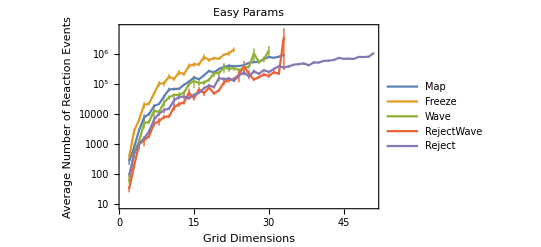

```mathematica
ListLogPlot[{MapColoringDataEasy,FreezeColoringDataEasy,WaveColoringDataEasy,RejectWaveColoringDataEasy,RejectColoringDataEasy},Joined->True,PlotRange->All,PlotLegends->{"Map","Freeze","Wave","RejectWave","Reject"},Frame->True,FrameLabel->{"Grid Dimensions","Average Number of Reaction Events"},PlotLabel->"Easy Params"]
```

```mathematica
MapColoringDataMedium=CollectColoringStats[SurfaceMapColoringCRN[3],MapColoringRules[3],3,25,10,{0.25,0.7}]
```

{{1,0.},{2,430.67.},{3,1826.287.},{4,7.51.510^3},{5,1.440.2010^4},{6,3.90.910^4},{7,7.81.910^4},{8,1.280.2410^5},{9,2.60.710^5},{10,4.21.110^5},{11,3.80.910^5},{12,2.31.310^6}}

```mathematica
FreezeColoringDataMedium=CollectColoringStats[SurfaceFreezeColoringCRN[3,10],FreezeColoringRules[3],3,25,10,{0.25,0.7}]
```

{{1,0.},{2,836.218.},{3,2966.430.},{4,2.00.710^4},{5,6.51.210^4},{6,2.20.710^5},{7,3.51.510^5},{8,6.72.710^5},{9,8.5.10^6}}

```mathematica
WaveColoringDataMedium=CollectColoringStats[SurfaceWaveColoringCRN[3,0.5],WaveColoringRules[3],3,25,10,{0.25,0.7}]
```

{{1,0.},{2,132.37.},{3,396.77.},{4,4.01.210^3},{5,9.31.810^3},{6,1.80.410^4},{7,5.12.410^4},{8,1.80.510^5},{9,1.130.2910^5},{10,3.60.910^5},{11,9.4.10^5},{12,4.01.710^6}}

```mathematica
RejectWaveColoringDataMedium=CollectColoringStats[SurfaceRejectWaveColoringCRN[3,0.01,10],RejectWaveColoringRules[3],3,25,10,{0.25,0.7}]
```

{{1,0.},{2,44.6.},{3,463.123.},{4,1237.495.},{5,8.72.610^3},{6,1.110.1910^4},{7,3.11.510^4},{8,3.60.810^4},{9,4.20.710^4},{10,2.60.810^5},{11,2.81.210^5},{12,1.30.910^6},{13,3.30.610^5},{14,5.32.310^5},{15,4.70.910^5},{16,2.81.710^6}}

```mathematica
RejectColoringDataMedium=CollectColoringStats[SurfaceRejectColoringCRN[3,0.1,100],RejectColoringRules[3],3,25,10,{0.25,0.7}]
```

{{1,0.},{2,100.16.},{3,1054.335.},{4,2.81.010^3},{5,4.71.210^3},{6,1.60.410^4},{7,3.31.610^4},{8,4.00.910^4},{9,7.62.010^4},{10,1.030.1810^5},{11,2.10.810^5},{12,2.80.710^5},{13,4.91.410^5},{14,4.00.810^5},{15,10.03.110^5},{16,7.31.310^5},{17,8.11.510^5},{18,9.71.810^5},{19,1.60.510^6}}

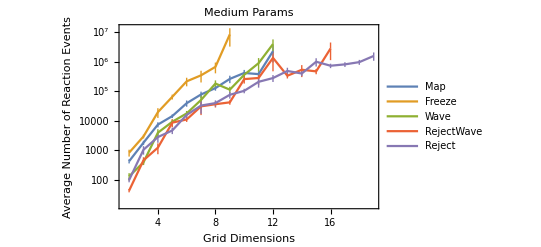

```mathematica
ListLogPlot[{MapColoringDataMedium,FreezeColoringDataMedium,WaveColoringDataMedium,RejectWaveColoringDataMedium,RejectColoringDataMedium},Joined->True,PlotRange->All,PlotLegends->{"Map","Freeze","Wave","RejectWave","Reject"},Frame->True,FrameLabel->{"Grid Dimensions","Average Number of Reaction Events"},PlotLabel->"Medium Params"]
```

```mathematica
MapColoringDataHard=CollectColoringStats[SurfaceMapColoringCRN[3],MapColoringRules[3],3,25,10,{0.3,0.9}]
```

{{1,0.},{2,469.79.},{3,3625.611.},{4,9.41.710^3},{5,3.60.710^4},{6,1.290.2810^5},{7,3.41.210^5},{8,1.60.710^6}}

```mathematica
FreezeColoringDataHard=CollectColoringStats[SurfaceFreezeColoringCRN[3,10],FreezeColoringRules[3],3,25,10,{0.3,0.9}]
```

{{1,0.},{2,971.195.},{3,4389.684.},{4,2.30.510^4},{5,1.50.410^5},{6,3.40.710^5},{7,1.80.410^6}}

```mathematica
WaveColoringDataHard=CollectColoringStats[SurfaceWaveColoringCRN[3,0.5],WaveColoringRules[3],3,25,10,{0.3,0.9}]
```

{{1,0.},{2,182.39.},{3,1145.394.},{4,4584.977.},{5,2.50.410^4},{6,9.93.410^4},{7,4.71.110^5},{8,3.71.510^6}}

```mathematica
RejectWaveColoringDataHard=CollectColoringStats[SurfaceRejectWaveColoringCRN[3,0.01,10],RejectWaveColoringRules[3],3,25,10,{0.3,0.9}]
```

{{1,0.},{2,60.7.},{3,448.83.},{4,4.21.110^3},{5,1.030.2210^4},{6,2.60.510^4},{7,1.070.2310^5},{8,4.81.910^5},{9,1.400.2510^6},{10,5.31.210^6}}

```mathematica
RejectColoringDataHard=CollectColoringStats[SurfaceRejectColoringCRN[3,0.1,100],RejectColoringRules[3],3,25,10,{0.3,0.9}]
```

{{1,0.},{2,181.24.},{3,632.129.},{4,4890.999.},{5,2.60.910^4},{6,5.41.610^4},{7,6.31.310^4},{8,3.20.610^5},{9,5.91.910^5},{10,8.01.410^5},{11,1.400.2710^6}}

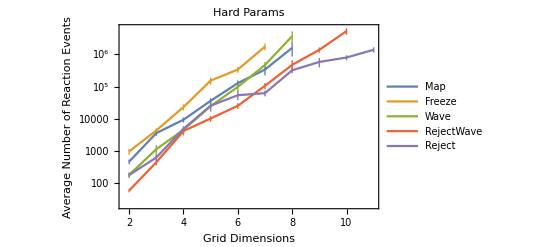

```mathematica
ListLogPlot[{MapColoringDataHard,FreezeColoringDataHard,WaveColoringDataHard,RejectWaveColoringDataHard,RejectColoringDataHard},Joined->True,PlotRange->All,PlotLegends->{"Map","Freeze","Wave","RejectWave","Reject"},Frame->True,FrameLabel->{"Grid Dimensions","Average Number of Reaction Events"},PlotLabel->"Hard Params"]
```

Are we beginning to see a qualitative difference in complexity scaling for SurfaceRejectColoringCRN at grid sizes 10 and larger, compared to the others?   It is hard to say from this data: the last SurfaceRejectWaveColoringCRN may be an anomaly; due to the data collection routine’s stopping criterion, one tends to stop after an unusually difficulty round.

General concern: During debugging, I’ve seen some CRNs get stuck before a valid solution has been found.  For each CRN, still must logically verify that if the CRN halts, it represents a valid coloring.  And also include a verification by SAT during the timing runs above.

It would be nice to compare number of reaction events and actual real running time for surface CRNs and well-mixed CRNs on the same graph.

If we want to use the same surface CRN for solving arbitrary graph coloring problems, rather than just planar ones, we can use the same trick used for the surface CRN SAT-solver: use just a few layers of 3D so that the wires (i.e. vertex regions) can easily cross.  No change in the CRN would be needed.   In fact, the layout is super straightforward:  for n vertices, just make a grid of n vertical on layer 1 and n horizontal lines on layer 4, connected solidly along the diagonal, and having an edge-pair on off-diagonal crossings to connect the regions.  Thus, each “vertex” is a vertical/horizontal line pair that cross along the diagonal.  These wiry regions will have to each be solidly colored, so edge mismatches will lead to a basically 1D random walk recoloring... not very effective because it will take O(n^2) time to complete a recoloring, with O(1/n) probability of success.    This is the same issue that lead to inefficiencies in the first 3-SAT surface CRN and lead to the burning potato design that transmitted signals in linear instead of quadratic time.  The same could be done here with graph coloring, and presumably could convert the O(n^2) recoloring time to just O(n).  That would be noticeable in practice, but pales in comparison to changing the exponent of time complexity for actually finding a solution, which is expected to be exponential in n.